```mathematica
1+1
```

2

```mathematica
<<"C:\\Users\\fsiano\\work\\dev\\workspace\\AD\\AD\\Kernel\\AD.m";
```

## Initialization

```mathematica
BlackScholesCall[s_,k_,σ_,r_,d_,t_]=1/2 Exp[-d t]s (Erf[((Sqrt[t] σ)/2+((r-d) t+Log[s/k])/(Sqrt[t] σ))/Sqrt[2]]+1)-1/2 Exp[-r t]  k (Erf[(((r-d) t+Log[s/k])/(Sqrt[t] σ)-(Sqrt[t] σ)/2)/Sqrt[2]]+1) ;
BlackScholesGamma[s_,k_,σ_,r_,d_,t_]=D[BlackScholesCall[s,k,σ,r,d,t], {s,2}]//FullSimplify ;
sT[s_,σ_,r_,d_,t_, random_]:=s Exp[(r-d-1/2 σ^2) t] Exp[σ Sqrt[t] random]
```

```mathematica
sm[x_,ϵ_]=2 ϵ PDF[NormalDistribution[0, Sqrt[2 ϵ]],x] + x CDF[NormalDistribution[0, Sqrt[2 ϵ]],x] ;
dd[x_,ϵ_]=PDF[NormalDistribution[0, Sqrt[2 ϵ]],x] ;
```

## Black-Scholes

```mathematica
TableForm[{BlackScholesCall[50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,1,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,1,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,0,1,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,0,0,1,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,0,0,0,1][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[2,0,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,1,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,1,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,1,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,0,1,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,0,0,1][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75]
}, TableHeadings->{{"value", "d_s0","d_strike","d_vol", "d_ir","d_yield","d_bigT", "d_s0_s0", "d_s0_strike", "d_s0_vol","d_s0_ir","d_s0_yield","d_s0_bigT"}}]
```

value | 8.89865
d_s0 | 0.630232
d_strike | -0.459613
d_vol | 16.3459
d_ir | 16.9597
d_yield | -23.6337
d_bigT | 6.03441
d_s0_s0 | 0.0193729
d_s0_strike | -0.0196879
d_s0_vol | 0.0480192
d_s0_ir | 0.726483
d_s0_yield | -1.19916
d_s0_bigT | 0.062838

```mathematica
BlackScholesCall[fd[50.0, <|"s0"->1|>], fd[49.2,<|"strike"->1|>],fd[0.45,<|"vol"->1|>], fd[0.05,<|"ir"->1|>], fd[0.0, <|"yield"->1|>],fd[0.75, <|"bigT"->1|>]]
```

fd[8.89865,<|vol→16.3459,bigT→6.03441,strike→-0.459613,s0→0.630232,yield→-23.6337,ir→16.9597|>]

```mathematica
fd[8.898647185376067,<|"vol"->16.34587698121761,"bigT"->6.034411591762857,"strike"->-0.45961321032421676,"s0"->0.6302323426665506,"yield"->-23.633712849995653,"ir"->16.959727460963606|>]
```

fd[8.89865,<|vol→16.3459,bigT→6.03441,strike→-0.459613,s0→0.630232,yield→-23.6337,ir→16.9597|>]

```mathematica
Derivative[1,0,0,0,0,0][BlackScholesCall][fd[50.0, <|"s0"->1|>], fd[49.2,<|"strike"->1|>],fd[0.45,<|"vol"->1|>], fd[0.05,<|"ir"->1|>], fd[0.0, <|"yield"->1|>],fd[0.75, <|"bigT"->1|>]]
```

fd[0.630232,<|s0→0.0193729,ir→0.726483,bigT→0.062838,vol→0.0480192,strike→-0.0196879,yield→-1.19916|>]

```mathematica
fd[0.6302323426665508,<|"s0"->0.019372891236998653,"ir"->0.7264834213874491,"bigT"->0.06283798626164605,"vol"->0.048019193897165025,"strike"->-0.019687897598575862,"yield"->-1.1991576783873625|>]
```

```mathematica
Derivative[2,0,0,0,0,0][BlackScholesCall][fd[50.0, <|"s0"->1|>], fd[49.2,<|"strike"->1|>],fd[0.45,<|"vol"->1|>], fd[0.05,<|"ir"->1|>], fd[0.0, <|"yield"->1|>],fd[0.75, <|"bigT"->1|>]]
```

```mathematica
fd[0.019372891236998667,<|"s0"->-0.0007180040122684912,"strike"->0.0003359209222850798,"yield"->-0.002134186395429582,"ir"->-0.01239548203231943,"bigT"->-0.013987421739454171,"vol"->-0.04387018756877626|>]
```

```mathematica
sims=Module[{s0=50.0, strike=49.2, vol=0.45, ir=0.05, yield=0.0,bigT=0.75, nSims=10^3, rvs,paths, payoff, delta},
SeedRandom[123];
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff=Exp[-ir bigT]sm[paths-strike, 0.005];
delta=Exp[-ir bigT] 1/2 Erfc[-((paths-strike)/(2 Sqrt[0.005]))] paths/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff, delta}
];
```

```mathematica
(* PV *)
{Mean[sims[[1]]], StandardDeviation[sims[[1]]] / Sqrt[Length[sims[[1]]]]}
```

{8.31979,0.474683}

```mathematica
(* Delta *)
{Mean[sims[[2]]], StandardDeviation[sims[[2]]] / Sqrt[Length[sims[[2]]]]}
```

{0.610494,0.021932}

```mathematica
sims=Module[{s0=fd[50.0, <|"s0"->1|>], strike=fd[49.2,<|"strike"->1|>], vol=fd[0.45,<|"vol"->1|>], ir=fd[0.05,<|"ir"->1|>], yield=fd[0.0, <|"yield"->1|>],bigT=fd[0.75, <|"bigT"->1|>], nSims=10^3, rvs,paths, payoff, delta},
SeedRandom[123];
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff=Exp[-ir bigT]sm[paths-strike, 0.005];
delta=Exp[-ir bigT] 1/2 Erfc[-((paths-strike)/(2 Sqrt[0.005]))] paths/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff, delta}
];
```

```mathematica
(* PV *)
Mean[sims[[1]]]
recursiveStatistics[sims[[1]]]
```

fd[8.31979,<|strike→-0.451322,vol→14.9839,bigT→5.60543,yield→-22.8935,ir→16.6537,s0→0.610494|>]

{fd[8.31979,<|strike→-0.451322,vol→14.9839,bigT→5.60543,yield→-22.8935,ir→16.6537,s0→0.610494|>],fd[0.474446,<|strike→-0.00897592,vol→1.2659,bigT→0.401852,yield→-0.687048,ir→0.331214,s0→0.0183213|>]}

```mathematica
(* Delta *)
Mean[sims[[2]]]
recursiveStatistics[sims[[2]]]
```

fd[0.610494,<|strike→-0.0149573,vol→0.0886069,bigT→0.063398,yield→-1.01011,ir→0.552239,s0→0.0147264|>]

{fd[0.610494,<|strike→-0.0149573,vol→0.0886069,bigT→0.063398,yield→-1.01011,ir→0.552239,s0→0.0147264|>],fd[0.021921,<|strike→0.0000310073,vol→0.0183197,bigT→0.00542027,yield→-0.0153061,ir→-0.00113463,s0→-0.0000302569|>]}

```mathematica
1-0.018830573493830043/0.019372891236998663
```

```mathematica
1-8.684181416829889/8.898647185376067
```

```mathematica
sims=Module[{s0=fd[50.0, <|s0->1|>], strike=fd[49.2,<|strike->1|>], vol=fd[0.45,<|vol->1|>], ir=fd[0.05,<|ir->1|>], yield=fd[0.0, <|yield->1|>],bigT=fd[0.75, <|bigT->1|>], nSims=10^4, nBuckets=10, rvs,paths, payoff, delta},
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff[p_]:=Exp[-ir bigT]sm[p-strike, 0.005];
delta[p_]:=Exp[-ir bigT] 1/2 Erfc[-((p-strike)/(2 Sqrt[0.005]))] p/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff[paths], delta[paths], payoff[#] & /@ Partition[paths, nSims/nBuckets], delta[#] & /@ Partition[paths, nSims/nBuckets]}
];
```

```mathematica
Mean[sims[[1]]]
```

fd[8.90852,<|strike→-0.459684,vol→16.2933,bigT→6.0188,yield→-23.6436,ir→16.9622,s0→0.630495|>]

```mathematica
Mean[sims[[2]]]
```

fd[0.630495,<|strike→-0.0232227,vol→-0.00331459,bigT→0.056128,yield→-1.32971,ir→0.856835,s0→0.0228489|>]

```mathematica
recursiveStatistics[sims[[1]]]
```

```mathematica
recursiveStatistics[sims[[2]]]
```

```mathematica
recursiveStatistics[recursiveStatistics[#] & /@ sims[[3]]]
```

```mathematica
recursiveStatistics[recursiveStatistics[#] & /@ sims[[4]]]
```

```mathematica
sims=Module[{s0=fd[50.0, <|s0->1|>], strike=fd[49.2,<|strike->1|>], vol=fd[0.45,<|vol->1|>], ir=fd[0.05,<|ir->1|>], yield=fd[0.0, <|yield->1|>],bigT=fd[0.75, <|bigT->1|>], nSims=10^4, rvs,paths, payoff, delta},
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff=Exp[-ir bigT]sm[paths-strike, 0.005];
delta=Exp[-ir bigT] 1/2 Erfc[-((paths-strike)/(2 Sqrt[0.005]))] paths/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff, delta}
];
```

```mathematica
Remove[pv, delta, valuation]
pv[s_,k_,σ_,r_,d_,t_,  rvs_]:=Exp[-r t] sm[sT[s, σ, r, d, t, rvs]-k, 0.005]
delta[s_,k_,σ_,r_,d_,t_,  rvs_]:=Derivative[1, 0,0,0,0,0,0][pv][s,k,σ,r,d,t,  rvs]
valuation[s_,k_,σ_,r_,d_,t_,  rvs_]:={pv[s,k,σ,r,d,t,  rvs], delta[s,k,σ,r,d,t,  rvs]}
```

```mathematica
rvs= RandomVariate[NormalDistribution[0,1], {2}];
```

```mathematica
pv[50.0, 49.2,0.45,0.05,0.0,0.75, rvs]
```

```mathematica
pv[fd[50.0, <|s0->1|>],  fd[49.2,<|strike->0|>], fd[0.45,<|vol->1|>], fd[0.05,<|ir->1|>], fd[0.0, <|yield->1|>],fd[0.75, <|bigT->1|>], rvs]
```

```mathematica
recursiveStatistics /@ valuation[fd[50.0, <|s0->1|>],  fd[49.2,<|strike->1|>], fd[0.45,<|vol->1|>], fd[0.05,<|ir->1|>], fd[0.0, <|yield->1|>],fd[0.75, <|bigT->1|>], rvs]
```

```mathematica
1-0.6358062897035217/0.6302323426665506
```

```mathematica
1-0.021137877396396637/0.019372891236998663
```

## Bachelier

```mathematica
bachelierValue[cp_,  f_, k_, σ_, r_, t_]=Exp[-r t] cp ((f-k) (HeavisideTheta[cp]-CDF[NormalDistribution[0, 1], (k-f)/(σ √t)])+ σ √t PDF[NormalDistribution[0, 1], (k-f)/(σ √t)]);
```

```mathematica
bachelierValue[1, 50, 50, 0.1, 0.00, 1]
```

0.0398942

```mathematica
Derivative[0, 1,0,0,0,0][bachelierValue][1, 50, 50, 0.1, 0.00, 1]
```

0.5

```mathematica
Derivative[0, 0,0,1,0,0][bachelierValue][1, 50, 50, 0.1, 0.00, 1]
```

0.398942

```mathematica
bachelierValue[1, fd[50, <|f->1|>], 50, fd[0.1, <|σ->1|>], 0.00, 1]
```

fd[0.0398942,<|f→0.5,σ→0.398942|>]

## Work

### Examples

```mathematica
fd[1.23, 5.67]
```

fd[1.23,5.67]

```mathematica
fd[x1, <|x1->y1|>]
```

fd[x1,<|x1→y1|>]

```mathematica
fd[x1, <|x1->y1|>]+3
```

fd[3+x1,<|x1→y1|>]

```mathematica
-2fd[x1, <|x1->y1|>]
```

fd[-2 x1,<|x1→-2 y1|>]

```mathematica
fd[x1, <|x1->y1|>]+fd[x2, <|x2->y2|>]
```

fd[x1+x2,<|x1→y1,x2→y2|>]

```mathematica
fd[expr1, <|x1->y1, x3->y3|>]+fd[expr2, <|x2->y2, x4->y4|>]
```

fd[expr1+expr2,<|x1→y1,x3→y3,x2→y2,x4→y4|>]

```mathematica
fd[expr1+expr2,<|x1->y1,x3->y3,x2->y2,x4->y4|>]
```

fd[expr1+expr2,<|x1→y1,x3→y3,x2→y2,x4→y4|>]

```mathematica
fd[expr1, <|x1->y1, x3->y3|>] fd[expr2, <|x2->y2, x4->y4|>]
```

fd[expr1 expr2,<|x1→expr2 y1,x3→expr2 y3,x2→expr1 y2,x4→expr1 y4|>]

```mathematica
fd[x1, <|x1->y1|>]^(-2)
```

fd[1/x1^2,<|x1→-(2 y1)/x1^3|>]

```mathematica
fd[Tan[x1], <|x1-> y1|>]+fd[x2, <|x2->y2|>]
```

fd[x2+Tan[x1],<|x2→y2,x1→y1|>]

```mathematica
fd[x1, <|x1->y1|>]+fd[x2, <|x2->y2|>]
```

```mathematica
fd[x1, <|x1->y1|>]+3fd[x2, <|x2->y2|>]
```

```mathematica
fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]
```

```mathematica
Sin[fd[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]
```

```mathematica
fd[Sin[x1 x2],<|x1->x2 y1 Cos[x1 x2],x2->x1 y2 Cos[x1 x2]|>]
```

```mathematica
fd[x3, <|x3->y3|>] Sin[fd[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]
```

```mathematica
Exp[fd[x3, <|x3->y3|>] Sin[fd[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]]
```

```mathematica
Exp[fd[x2, <|x2->y2|>] Sin[fd[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]]
```

```mathematica
Exp[fd[x3, <|x3->y3|>] Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]]]
```

```mathematica
D[Exp[x3 Sin[x1 x2]], {{x1, x2, x3}}]
```

```mathematica
Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]] Cos[fd[x3, <|x3->y3|>] fd[x4, <|x4->y4|>]^3] (Log[Tan[fd[x5, <|x5-> y5|>]/fd[x6, <|x6->y6|>]]])^(-2)
```

```mathematica
Trace[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]]//MatrixForm
```

```mathematica
With[{local=Exp[fd[x3, <|x3->y3|>] Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]]]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
With[{local=D[Exp[x3 Sin[x1 x2]], {{x1, x2, x3}}]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
With[{local=Tan[Exp[fd[x3, <|x3->y3|>] Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]]]+Log[fd[x3, <|x3->y3|>] fd[x1, <|x1->y1|>]]]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
With[{local=D[Tan[Exp[x3] Sin[x1 x2]+Log[x3 x1]], {{x1, x2, x3}}]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
Sin[fd[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]
```

```mathematica
traceView2[ D[Sin[x1+x2],{{x1,x2}}]]
```

```mathematica
D[Sin[x1+x2],{{x1,x2}}]//Grap
```

```mathematica
traceView2[Sin[fd[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]]
```

```mathematica
traceView2[D[Sin[x1 x2], {{x1, x2}}]]
```

```mathematica
traceView2[Tan[Exp[fd[x3, <|x3->y3|>] Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]]]+Log[fd[x3, <|x3->y3|>] fd[x1, <|x1->y1|>]]]]
```

```mathematica
traceView2[D[Tan[Exp[x3] Sin[x1 x2]+Log[x3 x1]], {{x1, x2, x3}}]]
```

```mathematica
traceView2[Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]] Cos[fd[x3, <|x3->y3|>] fd[x4, <|x4->y4|>]^3] (Log[Tan[fd[x5, <|x5-> y5|>]/fd[x6, <|x6->y6|>]]])^(-2)]
```

```mathematica
traceView2[D[Sin[x1 x2] Cos[x3 x4^3] (Log[Tan[x5/x6]])^(-2),{{x1,x2,x3,x4,x5,x6}}]]
```

```mathematica
LeafCount[fd[x1, <|x1->y1|>] + fd[x1, <|x1->y1|>]]
```

```mathematica
LeafCount[D[x1+x2,{{x1, x2}}]]
```

```mathematica
LeafCount[Sin[fd[x1, <|x1->y1|>] + fd[x1, <|x1->y1|>]]]
```

```mathematica
LeafCount[D[Sin[x1+x2],{{x1, x2}}]]
```

```mathematica
LeafCount[Sin[fd[x1, <|x1->y1|>] fd[x2, <|x2->y2|>]] Cos[fd[x3, <|x3->y3|>] fd[x4, <|x4->y4|>]^3] (Log[Tan[fd[x5, <|x5-> y5|>]/fd[x6, <|x6->y6|>]]])^(-2)]
```

```mathematica
LeafCount[D[Sin[x1 x2] Cos[x3 x4^3] (Log[Tan[x5/x6]])^(-2),{{x1,x2,x3,x4,x5,x6}}]]
```

```mathematica
Mean[{fd[x1, <|x1-> y1|>], fd[x2, <|x2-> y2|>], fd[x3, <|x3-> y3|>]}]
```

```mathematica
StandardDeviation[{fd[x1, <|x1-> y1|>], fd[x2, <|x2-> y2|>], fd[x3, <|x3-> y3|>]}] /. Conjugate[z_] -> z
```

```mathematica
m={{fd[x1, <|x1-> y1|>], fd[x2, <|x2-> y2|>]},{fd[x3, <|x3-> y3|>], fd[x4, <|x4-> y4|>]}};
```

```mathematica
m//MatrixForm
```

```mathematica
Tr[m]
```

```mathematica
Det[m]
```

```mathematica
Inverse[m] //MatrixForm
```

```mathematica
fd[1.23, <|x1->y1|>]+fd[4.56, <|x2-> y2|>]
```

```mathematica
fd[1.23, <|x1->y1|>] fd[4.56, <|x2-> y2|>]
```

```mathematica
Log[Sin[fd[1.23, <|x1->y1|>]]]
```

```mathematica
Derivative[1][Log[Sin[#]]&][1.23]
```

```mathematica
fd[1.23, <|x1->y1, x3->y3|>]+fd[4.56, <|x2-> y2|>]
```

```mathematica
fd[1.23, <|x1->y1, x3->y3|>] fd[4.56, <|x2-> y2|>]
```

```mathematica
counter=0;
out=fd[x,<|x->y|>];
While[
counter<4, 
out=Sin[out];
counter++
]
```

```mathematica
out
```

```mathematica
Solve[fd[a,<|a->ya|>] x^2+fd[b,<|b->yb|>] x+fd[c,<|c->yc|>]==0,x]
```

```mathematica
psi=PseudoInverse[{{fd[1, <|x1->y1|>], fd[2, <|x2->y2|>], fd[3, <|x3->y3|>]}, {fd[4, <|x4->y4|>], fd[5, <|x5->y5|>], fd[6, <|x6->y6|>]}, {fd[7, <|x7->y7|>], fd[8, <|x8->y8|>], fd[9, <|x9->y9|>]}}];
```

```mathematica
Conjugate[fd[5,<|x5->y5|>]]
```

```mathematica
Conjugate[fd[5,<|x5->y5|>]] /. toValue[z_]
```

```mathematica
fd[5,<|x5->y5|>]// toValue
```

```mathematica
Solve[fd[a,<|a->ya|>] x^2+fd[b,<|b->yb|>] x+fd[c,<|c->yc|>]==0,x]//toValue
```

```mathematica
fd[x1, <|x1->y1|>]^fd[x2, <|x2->y2|>]
```

```mathematica
fd[x1, <|x1->y1|>]^fd[x2, <|x2->y2|>]
```

```mathematica
E^fd[x,<|x->y|>]
```

```mathematica
Exp[fd[x,<|x->y|>]]
```

```mathematica
fd[x1,<|x1->y1|>] fd[x2,<|x2->y2|>]
```

```mathematica
D[x1 x2,{{x1, x2}}]
```

```mathematica
fd[1.23,<|x1->y1|>] fd[4.56,<|x2->y2|>]
```

```mathematica
propagatefd[ff, {expr1, expr2}, {<|x1->y1, x2->y2|>, <|x3->y3|>}]
```

```mathematica
propagatefd[ff, {expr1, expr2}, {<|x1->y1, x2->y2|>, <|x2->y3|>}]
```

```mathematica
KeyUnion[{<|x1->y1, x2->y2|>, <|x2->y3|>}]
```

```mathematica
Merge[{<|a->1,b->2|>,<|b->4,c->5|>},Total]
```

```mathematica
Merge[<|a->1,b->2|>]
```

```mathematica
Sin[fd[x+I y, <|x1->y1, x2->y2|>]]
```

### Graphs

\[Theta]={Subscript[\[Theta], 1], Subscript[\[Theta], 2]}
nM= 3 - time steps
nMC=4  - simulations

```mathematica
nE=3;
nMC=2;
```

```mathematica
x0=Table[Subscript[x, 0,m], {m, nE}]
```

{x_(0,1),x_(0,2),x_(0,3)}

```mathematica
spot=Table[Subscript[x, m]^n,{n, ToString /@Range[nMC]}, {m, ToString /@Range[nE]}];
```

```mathematica
spot
```

{{x_1^1,x_2^1,x_3^1},{x_1^2,x_2^2,x_3^2}}

```mathematica
vol=Table[Subscript[σ, n], {n, ToString /@Range[nE]}]
```

{σ_1,σ_2,σ_3}

```mathematica
cashE=Table[Subscript["E", m]^n,{n, ToString /@Range[nMC]}, {m, ToString /@Range[nE]}];
```

```mathematica
continuationH=Table[Subscript["H", m]^n,{n, ToString /@Range[nMC]}, {m, ToString /@Range[nE]}];
```

```mathematica
beta=Table[Subscript[β, n], {n, ToString /@Range[nE-1]}];
```

```mathematica
(*graphSpotProcess=Flatten[Thread[#[[1]]-> #[[2]]]& /@ Partition[Join[{x0}, Transpose[spot]], 2, 1], 1];*)
```

```mathematica
values=Table[Subscript[V, n]^m, {n, ToString /@Range[nE]}, {m,  ToString /@Range[nMC]}];
```

```mathematica
graphSpotProcess=Flatten[Thread[#[[1]]->#[[2;;]]] & /@ Transpose[Join[{x0}, spot]]];
```

```mathematica
graphVol=Flatten[(Thread@@{vol->  #}) & /@ spot, 1];
```

```mathematica
graphcashE=Flatten[MapThread[Thread[#1-> #2] &, {spot, cashE}],1];
```

```mathematica
(*graphcontinuationH=Flatten[MapThread[Thread[#1->#2] &, {spot, continuationH}],1];*)
```

```mathematica
graphcontinuationH=Join[Flatten[MapThread[Thread[#1->#2] &, {Transpose[spot][[1;;-2]], Transpose[continuationH][[1;;-2]]}],1],Flatten[MapThread[Thread[#1->#2]&, {beta, Transpose[continuationH][[1;;-2]]}], 1]];
```

```mathematica
graphBeta=Join[Flatten[MapThread[Thread[#1->#2]&,{Transpose[spot][[1;;-2]], beta}], 1], Flatten[MapThread[Thread[#1->#2] &, {values[[2;;]], beta}]]]
```

{x_1^1→β_1,x_1^2→β_1,x_2^1→β_2,x_2^2→β_2,V_2^1→β_1,V_2^2→β_1,V_3^1→β_2,V_3^2→β_2}

```mathematica
graphvalues=Join[Flatten[MapThread[Thread[#1->#2]&, {Transpose[cashE], values}], 1],Flatten[MapThread[Thread[#1->#2]&, {Transpose[continuationH][[1;;-2]], values[[1;;-2]]}], 1] ,Flatten[Thread[#[[1]]-> #[[2]]] & /@ Partition[Reverse[values], 2, 1], 1] ];
```

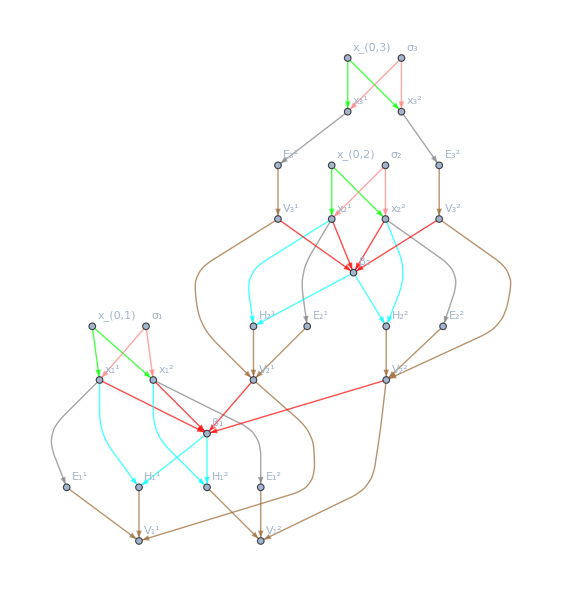

```mathematica
mess=Graph[Join[graphSpotProcess, graphVol, graphcashE, graphcontinuationH, graphBeta, graphvalues], VertexLabels-> "Name", EdgeStyle-> Join[Thread[graphSpotProcess->  Green], Thread[graphVol->  Pink],Thread[graphcashE->  Gray], Thread[graphcontinuationH->  Cyan], Thread[graphBeta-> Red], Thread[graphvalues-> Brown]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"UserGuide", "graph.pdf"}], mess]
```

C:\Users\fsiano\work\dev\workspace\AD\UserGuide\graph.pdf

## Test Bermudan

```mathematica
assocToTable[a_Association]:=TableForm[Values[a], TableHeadings->{Keys[a]}]
```

### Bermudan

#### Inputs

```mathematica
elapsedStart=Date[];
SeedRandom[123];
nE=30;
nMC=10^1;
nB=5;
rvs=RandomVariate[NormalDistribution[0, 1] ,{nMC, nE}];
forward=23.0+10 Sin[2 π Range[nE]/60];
(*forward=fd[#, <|Unique["fc"]->1|>] & /@ forward;*)
forward=MapThread[fd[#1, <|#2->1|>]&,{forward, "fc"<>ToString[#] & /@ Range[nE]}];
sigma = 0.45;
(*tv=Sqrt[Range[nE]/365.242 fd[0.45, <|Unique["vol"]->1|>]^2];*)
(*tv=Sqrt[Range[nE]/365.242]  (fd[sigma, <|Unique["vol"]->1|>] & /@ Range[nE]);*)
tv=Sqrt[Range[nE]/365.242] MapThread[fd[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];
spot=simulationSpot[forward, tv, rvs ];

irt = 0.0245 Range[1/ 365.242, nE/365.242, 1/365.242] & /@ Range[nMC];
numeraire=Exp[irt];

(*strike=RandomReal[MinMax[Flatten[spot[[All, All, 1]]]]];*)
strike=Mean[Flatten[spot[[All, All, 1]]]];

exerciseValue=Map[payoffBermudean[#, strike] &,spot, {2}];

basisFunctions = Function[x,Evaluate@Table[LaguerreL[n,x], {n,nB}]];

phi = basisFunctions[spot];
elapsedEnd=Date[];
```

```mathematica
DateDifference[elapsedStart, elapsedEnd, "Second"]
```

8.22082 s

```mathematica
forward
```

{fd[24.0453,<|fc1→1|>],fd[25.0791,<|fc2→1|>],fd[26.0902,<|fc3→1|>],fd[27.0674,<|fc4→1|>],fd[28.,<|fc5→1|>],fd[28.8779,<|fc6→1|>],fd[29.6913,<|fc7→1|>],fd[30.4314,<|fc8→1|>],fd[31.0902,<|fc9→1|>],fd[31.6603,<|fc10→1|>],fd[32.1355,<|fc11→1|>],fd[32.5106,<|fc12→1|>],fd[32.7815,<|fc13→1|>],fd[32.9452,<|fc14→1|>],fd[33.,<|fc15→1|>],fd[32.9452,<|fc16→1|>],fd[32.7815,<|fc17→1|>],fd[32.5106,<|fc18→1|>],fd[32.1355,<|fc19→1|>],fd[31.6603,<|fc20→1|>],fd[31.0902,<|fc21→1|>],fd[30.4314,<|fc22→1|>],fd[29.6913,<|fc23→1|>],fd[28.8779,<|fc24→1|>],fd[28.,<|fc25→1|>],fd[27.0674,<|fc26→1|>],fd[26.0902,<|fc27→1|>],fd[25.0791,<|fc28→1|>],fd[24.0453,<|fc29→1|>],fd[23.,<|fc30→1|>]}

```mathematica
tv
```

{fd[0.0235463,<|vol1→0.052325|>],fd[0.0332995,<|vol2→0.0739988|>],fd[0.0407833,<|vol3→0.0906296|>],fd[0.0470925,<|vol4→0.10465|>],fd[0.0526511,<|vol5→0.117002|>],fd[0.0576764,<|vol6→0.12817|>],fd[0.0622976,<|vol7→0.138439|>],fd[0.0665989,<|vol8→0.147998|>],fd[0.0706388,<|vol9→0.156975|>],fd[0.0744599,<|vol10→0.165466|>],fd[0.0780941,<|vol11→0.173543|>],fd[0.0815667,<|vol12→0.181259|>],fd[0.0848973,<|vol13→0.188661|>],fd[0.0881021,<|vol14→0.195782|>],fd[0.0911943,<|vol15→0.202654|>],fd[0.0941851,<|vol16→0.2093|>],fd[0.0970838,<|vol17→0.215742|>],fd[0.0998984,<|vol18→0.221996|>],fd[0.102636,<|vol19→0.22808|>],fd[0.105302,<|vol20→0.234005|>],fd[0.107903,<|vol21→0.239783|>],fd[0.110442,<|vol22→0.245426|>],fd[0.112924,<|vol23→0.250942|>],fd[0.115353,<|vol24→0.256339|>],fd[0.117731,<|vol25→0.261625|>],fd[0.120063,<|vol26→0.266806|>],fd[0.12235,<|vol27→0.271889|>],fd[0.124595,<|vol28→0.276878|>],fd[0.126801,<|vol29→0.281779|>],fd[0.128968,<|vol30→0.286596|>]}

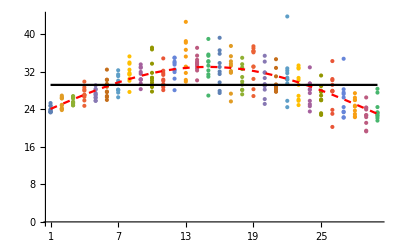

```mathematica
Which[NumericQ[forward[[1]]], 
Show[ListPlot[spot, Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle->Red], ListPlot[strike & /@ forward, PlotStyle->Black]]
, Head[forward[[1]]]==fd, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[spot[[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}]]
,True, "Check fc !"]
```

```mathematica
(*bigA=Outer[Total[#1 #2] &, basis, basis, 1,  1];*)
(*bigA=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,1;;-2]],{2,3,1}];*)bigA=Function[x,Outer[Total[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,1;;-2]],{2,3,1}];
```

```mathematica
bigA //Dimensions
```

{29,5,5}

```mathematica
bigA = Inverse /@ bigA;
bigA // Dimensions
```

{1,5,5}

```mathematica
phi[[All, All, -2]][[All, All, 1]]
```

{{-23.7517,-23.2275,-22.1973,-22.0535,-23.1711,-22.0938,-23.8149,-23.2646,-23.8558,-23.9182},{257.821,246.03,223.663,220.625,244.779,221.473,259.261,246.855,260.193,261.621},{-1681.63,-1561.36,-1341.89,-1312.98,-1548.78,-1321.03,-1696.53,-1569.68,-1706.21,-1721.06},{7269.62,6540.06,5266.,5104.02,6464.98,5148.99,7361.46,6589.8,7421.29,7513.32},{-21556.5,-18668.6,-13879.1,-13295.5,-18377.2,-13456.9,-21927.,-18862.3,-22169.1,-22542.8}}

```mathematica
(*bigB=Total[numeraire[[All,-2]]/numeraire[[All, -1]] values basis[[#, All]]]  & /@ Range[nB]*)
bigB=With[{day=-2},
seqsum[numeraire[[All,day]]/numeraire[[All,day+1]] exerciseValue[[All,day+1]] #]&/@phi[[All,All,day]]
];
```

```mathematica
Dot[bigA[[-2+1]], bigB]
```

{ad[15.5515,<|vol5→14.662,fc3→-42.8713,vol6→17.092,fc4→17.4331|>],ad[-2.33612,<|vol5→-21.0401,fc3→3.2307,vol6→-2.56768,fc4→-2.61869|>],ad[-0.399804,<|vol5→0.215665,fc3→0.40438,vol6→-0.439417,fc4→-0.448175|>],ad[0.0613036,<|vol5→0.268729,fc3→-0.190475,vol6→0.0674757,fc4→0.0686324|>],ad[0.00508123,<|vol5→-0.210122,fc3→-0.00143009,vol6→0.00561843,fc4→0.00566554|>]}

```mathematica
beta=Dot[Inverse[bigA], bigB]
```

```mathematica
Dot[beta, # ] & /@  Transpose[basis]
```

```mathematica
Dot[Transpose[basis], beta]
```

```mathematica
Dot[Dot[Inverse[Rationalize[bigA, 10^-3]], Rationalize[bigB, 10^-3]],  basis[[All, -1]]]
```

```mathematica
Dot[Dot[Inverse[Rationalize[bigA, 10^-4]], Rationalize[bigB, 10^-4]],  basis[[All, -1]]]
```

```mathematica
Dot[Dot[Inverse[Rationalize[bigA, 10^-6]], Rationalize[bigB, 10^-6]],  basis[[All, -1]]]
```

```mathematica
Function[x,Evaluate@Table[LaguerreL[n,x], {n, 5}]][spot] //Dimensions
```

```mathematica
AbsoluteTiming[1+1]
```

{3.84954×10^-6,2}

```mathematica
{elapsed, {bs, vs, hs}}=AbsoluteTiming[regressionCoefficient[Function[x,Evaluate@Table[LaguerreL[n,x], {n, nB}]],spot,numeraire,exerciseValue, exerciseValue[[All, -1]]]];
```

```mathematica
elapsed
```

368.81

```mathematica
vs //Dimensions
```

{30,10}

Reconcile day=-2

```mathematica
bigAm2=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,-2;;-2]],{2,3,1}];
```

```mathematica
bigAm2=bigAm2[[1]];
```

```mathematica
bigAm2//Dimensions
```

{5,5}

```mathematica
valuesFinal=exerciseValue[[All,-2+1]];
bigBm2=seqsum[numeraire[[All,-2]]/numeraire[[All,-2+1]] valuesFinal #]&/@phi[[All,All,-2]];
```

```mathematica
bigBm2//Dimensions
```

{5}

```mathematica
betam2=Dot[Inverse[bigAm2], bigBm2];
```

```mathematica
betam2//Dimensions
```

{5}

```mathematica
hm2=Dot[betam2, phi[[All, All, -2]]];
```

```mathematica
hm2//Dimensions
```

{10}

```mathematica
valuesFinal=MapThread[vf[#1,#2,#3]&,{exerciseValue[[All,-2]],hm2,numeraire[[All,-2]]/numeraire[[All,-2+1]] valuesFinal}];
```

```mathematica
betam2[[5]]
```

ad[0.,<|vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol28→0.,fc28→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>]

```mathematica
bs[[1]]
```

{ad[-2.33557×10^-31,<|vol29→-2.40168×10^-28,fc29→-1.88901×10^-29,vol30→-4.96874×10^-28,fc30→-4.85863×10^-29|>],ad[-8.21425×10^-32,<|vol29→-8.44736×10^-29,fc29→-6.63965×10^-30,vol30→-1.74751×10^-28,fc30→-1.70879×10^-29|>],ad[-1.76755×10^-32,<|vol29→-1.81816×10^-29,fc29→-1.42803×10^-30,vol30→-3.76031×10^-29,fc30→-3.67698×10^-30|>],ad[-2.5307×10^-33,<|vol29→-2.60306×10^-30,fc29→-2.04317×10^-31,vol30→-5.38387×10^-30,fc30→-5.26455×10^-31|>],ad[-1.99831×10^-34,<|vol29→-2.05341×10^-31,fc29→-1.61109×10^-32,vol30→-4.25123×10^-31,fc30→-4.15702×10^-32|>]}

Reconcile day=-3

```mathematica
bigAm3=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,-3;;-3]],{2,3,1}];
```

```mathematica
bigAm3=bigAm3[[1]];
```

```mathematica
bigAm3//Dimensions
```

{5,5}

```mathematica
bigBm3=seqsum[numeraire[[All,-3]]/numeraire[[All,-3+1]] valuesFinal #]&/@phi[[All,All,-3]];
```

```mathematica
betam3=Dot[Inverse[bigAm3], bigBm3];
```

```mathematica
betam3//Dimensions
```

{5}

```mathematica
hm3=Dot[betam3, phi[[All, All, -3]]];
```

```mathematica
hm3//Dimensions
```

{10}

```mathematica
valuesFinal=MapThread[vf[#1,#2,#3]&,{exerciseValue[[All,-3]],hm3,numeraire[[All,-3]]/numeraire[[All,-3+1]] valuesFinal}];
```

```mathematica
betam3
```

{ad[-0.0725133,<|vol28→-0.1107,fc28→0.172193,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[-0.000214013,<|vol28→-0.108328,fc28→-0.00822423,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.00150946,<|vol28→-0.0206598,fc28→-0.00426732,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[-0.000288786,<|vol28→-0.0034727,fc28→-0.000133445,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[-0.000132183,<|vol28→-0.000642653,fc28→0.0000185117,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>]}

```mathematica
bs[[2]]//TableForm
```

ad[-0.0673022,<|vol28→-0.102167,fc28→0.15846,vol29→2.9802×10^-29,fc29→2.35721×10^-30,vol30→6.31548×10^-29,fc30→6.17552×10^-30|>]
ad[-0.00012196,<|vol28→-0.0998054,fc28→-0.00764027,vol29→-2.4529×10^-32,fc29→-2.0178×10^-33,vol30→-5.66443×10^-32,fc30→-5.5389×10^-33|>]
ad[0.00139766,<|vol28→-0.0188,fc28→-0.00391961,vol29→-6.44663×10^-31,fc29→-5.10125×10^-32,vol30→-1.36747×10^-30,fc30→-1.33717×10^-31|>]
ad[-0.000266688,<|vol28→-0.00315763,fc28→-0.000118429,vol29→1.17865×10^-31,fc29→9.32196×10^-33,vol30→2.49732×10^-31,fc30→2.44198×10^-32|>]
ad[-0.000121284,<|vol28→-0.000595418,fc28→0.0000170308,vol29→5.46125×10^-32,fc29→4.32016×10^-33,vol30→1.15764×10^-31,fc30→1.13198×10^-32|>]

Reconcile day=-4

```mathematica
bigAm4=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,-4;;-4]],{2,3,1}];
```

```mathematica
bigAm4=bigAm4[[1]];
```

```mathematica
bigAm4//Dimensions
```

{5,5}

```mathematica
bigBm4=seqsum[numeraire[[All,-4]]/numeraire[[All,-4+1]] valuesFinal #]&/@phi[[All,All,-4]];
```

```mathematica
betam4=Dot[Inverse[bigAm4], bigBm4];
```

```mathematica
betam4//Dimensions
```

{5}

```mathematica
hm4=Dot[betam4, phi[[All, All, -4]]];
```

```mathematica
hm4//Dimensions
```

{10}

```mathematica
valuesFinal=MapThread[vf[#1,#2,#3]&,{exerciseValue[[All,-4]],hm4,numeraire[[All,-4]]/numeraire[[All,-4+1]] valuesFinal}];
```

```mathematica
betam4
```

{ad[0.75866,<|vol27→-19.524,fc27→-0.0243209,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-2.35924,fc28→-0.162533,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.228361,<|vol27→-6.07928,fc27→-0.0246977,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.679241,fc28→-0.0308982,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.0406455,<|vol27→-1.08761,fc27→-0.00625999,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.113158,fc28→-0.000984351,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.00459035,<|vol27→-0.122854,fc27→-0.000889123,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.0118198,fc28→0.000471615,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.000265266,<|vol27→-0.00721955,fc27→-0.0000659425,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.000632427,fc28→0.0000602494,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>]}

```mathematica
bs[[3]]//TableForm
```

ad[0.772138,<|vol27→-19.7453,fc27→-0.0237078,vol29→-2.08235×10^-28,fc29→-1.652×10^-29,vol30→-4.44985×10^-28,fc30→-4.35124×10^-29,vol28→-0.936444,fc28→0.370289|>]
ad[0.232313,<|vol27→-6.15539,fc27→-0.0251066,vol29→-6.34001×10^-29,fc29→-5.02937×10^-30,vol30→-1.35449×10^-28,fc30→-1.32447×10^-29,vol28→-0.234683,fc28→0.138606|>]
ad[0.0413096,<|vol27→-1.10054,fc27→-0.0063674,vol29→-1.13888×10^-29,fc29→-9.03434×10^-31,vol30→-2.43295×10^-29,fc30→-2.37903×10^-30,vol28→-0.026694,fc28→0.0322653|>]
ad[0.00466019,<|vol27→-0.124175,fc27→-0.000902642,vol29→-1.29471×10^-30,fc29→-1.02706×10^-31,vol30→-2.76586×10^-30,fc30→-2.70456×10^-31,vol28→-0.000999309,fc28→0.00465487|>]
ad[0.000269048,<|vol27→-0.00729442,fc27→-0.0000669481,vol29→-7.50923×10^-32,fc29→-5.95699×10^-33,vol30→-1.60422×10^-31,fc30→-1.56867×10^-32,vol28→0.000051324,fc28→0.000326315|>]

```mathematica
bs//Dimensions
```

{29,5}

```mathematica
Values[<|"vol28"->-0.10216705428319983,"fc28"->0.15845966521033006,"vol29"->2.980201245957065*^-29,"fc29"->2.3572054152826975*^-30,"vol30"->6.315478266316725*^-29,"fc30"->6.1755180480215595*^-30|>]
```

{-0.102167,0.15846,2.9802×10^-29,2.35721×10^-30,6.31548×10^-29,6.17552×10^-30}

```mathematica
bs[[2]]/. fd[expr_, a_] -> fd[expr, assocToTable[a]] //TableForm
```

ad[-0.0673022,vol28 | -0.102167
fc28 | 0.15846
vol29 | 2.9802×10^-29
fc29 | 2.35721×10^-30
vol30 | 6.31548×10^-29
fc30 | 6.17552×10^-30]
ad[-0.00012196,vol28 | -0.0998054
fc28 | -0.00764027
vol29 | -2.4529×10^-32
fc29 | -2.0178×10^-33
vol30 | -5.66443×10^-32
fc30 | -5.5389×10^-33]
ad[0.00139766,vol28 | -0.0188
fc28 | -0.00391961
vol29 | -6.44663×10^-31
fc29 | -5.10125×10^-32
vol30 | -1.36747×10^-30
fc30 | -1.33717×10^-31]
ad[-0.000266688,vol28 | -0.00315763
fc28 | -0.000118429
vol29 | 1.17865×10^-31
fc29 | 9.32196×10^-33
vol30 | 2.49732×10^-31
fc30 | 2.44198×10^-32]
ad[-0.000121284,vol28 | -0.000595418
fc28 | 0.0000170308
vol29 | 5.46125×10^-32
fc29 | 4.32016×10^-33
vol30 | 1.15764×10^-31
fc30 | 1.13198×10^-32]

```mathematica
vs[[1]]
```

{ad[0.0282095,<|vol29→-2.01067×10^-29,fc29→-1.59364×10^-30,vol30→-4.27903×10^-29,fc30→-4.1842×10^-30|>],ad[0.0282095,<|vol29→-6.2161×10^-30,fc29→-4.89732×10^-31,vol30→-1.30759×10^-29,fc30→-1.27861×10^-30|>],ad[0.0282095,<|vol29→-3.35963×10^-30,fc29→-2.63123×10^-31,vol30→-6.99119×10^-30,fc30→-6.83626×10^-31|>],ad[9.78300931981276×10^-974,<|vol30→2.63323363780108×10^-970,fc30→9.81968558723149×10^-971|>],ad[0.0282095,<|vol29→-1.40024×10^-29,fc29→-1.10775×10^-30,vol30→-2.96798×10^-29,fc30→-2.9022×10^-30|>],ad[0.0282095,<|vol29→-1.95953×10^-29,fc29→-1.55166×10^-30,vol30→-4.16077×10^-29,fc30→-4.06857×10^-30|>],ad[0.0282095,<|vol29→-2.4412×10^-30,fc29→-1.90281×10^-31,vol30→-5.03588×10^-30,fc30→-4.92428×10^-31|>],ad[0.0282095,<|vol29→-1.58492×10^-29,fc29→-1.25435×10^-30,vol30→-3.36189×10^-29,fc30→-3.28738×10^-30|>],ad[0.0282095,<|vol29→-1.39244×10^-29,fc29→-1.10156×10^-30,vol30→-2.95134×10^-29,fc30→-2.88593×10^-30|>],ad[0.0282095,<|vol29→-2.03153×10^-29,fc29→-1.60994×10^-30,vol30→-4.32185×10^-29,fc30→-4.22608×10^-30|>]}

```mathematica
bs[[2]] /. fd[expr_, a_] -> fd[expr, assocToTable[a]] //TableForm
```

ad[-0.0673022,vol28 | -0.102167
fc28 | 0.15846
vol29 | 2.9802×10^-29
fc29 | 2.35721×10^-30
vol30 | 6.31548×10^-29
fc30 | 6.17552×10^-30]
ad[-0.00012196,vol28 | -0.0998054
fc28 | -0.00764027
vol29 | -2.4529×10^-32
fc29 | -2.0178×10^-33
vol30 | -5.66443×10^-32
fc30 | -5.5389×10^-33]
ad[0.00139766,vol28 | -0.0188
fc28 | -0.00391961
vol29 | -6.44663×10^-31
fc29 | -5.10125×10^-32
vol30 | -1.36747×10^-30
fc30 | -1.33717×10^-31]
ad[-0.000266688,vol28 | -0.00315763
fc28 | -0.000118429
vol29 | 1.17865×10^-31
fc29 | 9.32196×10^-33
vol30 | 2.49732×10^-31
fc30 | 2.44198×10^-32]
ad[-0.000121284,vol28 | -0.000595418
fc28 | 0.0000170308
vol29 | 5.46125×10^-32
fc29 | 4.32016×10^-33
vol30 | 1.15764×10^-31
fc30 | 1.13198×10^-32]

```mathematica
bs[[3]] /. fd[expr_, a_] -> fd[expr, assocToTable[a]] //TableForm
```

ad[0.772138,vol27 | -19.7453
fc27 | -0.0237078
vol29 | -2.08235×10^-28
fc29 | -1.652×10^-29
vol30 | -4.44985×10^-28
fc30 | -4.35124×10^-29
vol28 | -0.936444
fc28 | 0.370289]
ad[0.232313,vol27 | -6.15539
fc27 | -0.0251066
vol29 | -6.34001×10^-29
fc29 | -5.02937×10^-30
vol30 | -1.35449×10^-28
fc30 | -1.32447×10^-29
vol28 | -0.234683
fc28 | 0.138606]
ad[0.0413096,vol27 | -1.10054
fc27 | -0.0063674
vol29 | -1.13888×10^-29
fc29 | -9.03434×10^-31
vol30 | -2.43295×10^-29
fc30 | -2.37903×10^-30
vol28 | -0.026694
fc28 | 0.0322653]
ad[0.00466019,vol27 | -0.124175
fc27 | -0.000902642
vol29 | -1.29471×10^-30
fc29 | -1.02706×10^-31
vol30 | -2.76586×10^-30
fc30 | -2.70456×10^-31
vol28 | -0.000999309
fc28 | 0.00465487]
ad[0.000269048,vol27 | -0.00729442
fc27 | -0.0000669481
vol29 | -7.50923×10^-32
fc29 | -5.95699×10^-33
vol30 | -1.60422×10^-31
fc30 | -1.56867×10^-32
vol28 | 0.000051324
fc28 | 0.000326315]

```mathematica
vs[[1]]
```

{{ad[0.294972,<|vol30→-0.382438,fc28→0.993586|>],ad[1.09208×10^-10,<|vol29→3.59978×10^-9,fc27→9.26522×10^-9,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[6.99885×10^-13,<|vol29→1.76499×10^-11,fc27→6.6855×10^-11,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[1.16733,<|vol30→1.57629,fc28→1.02839|>],ad[2.17658×10^-9,<|vol29→7.9723×10^-8,fc27→1.69532×10^-7,vol30→0.,fc28→0.|>],ad[0.0000218443,<|vol30→-0.00166039,fc28→0.00107791|>],ad[1.37723,<|vol30→2.05745,fc28→1.03676|>]},{ad[0.294972,<|vol30→-0.382438,fc28→0.993586|>],ad[1.09208×10^-10,<|vol29→3.59978×10^-9,fc27→9.26522×10^-9,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[6.99885×10^-13,<|vol29→1.76499×10^-11,fc27→6.6855×10^-11,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[1.16733,<|vol30→1.57629,fc28→1.02839|>],ad[2.17658×10^-9,<|vol29→7.9723×10^-8,fc27→1.69532×10^-7,vol30→0.,fc28→0.|>],ad[0.0000218443,<|vol30→-0.00166039,fc28→0.00107791|>],ad[1.37723,<|vol30→2.05745,fc28→1.03676|>]}}

```mathematica
hs
```

{{ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>]},{ad[36.7704,<|vol29→480.659,fc27→-95.8154,vol30→40.3802,fc28→41.2494|>],ad[-5.66861,<|vol29→-143.234,fc27→18.3861,vol30→-6.23679,fc28→-6.34852|>],ad[-78.9091,<|vol29→-1110.09,fc27→210.862,vol30→-86.6955,fc28→-88.4852|>],ad[-88.0973,<|vol29→-1220.12,fc27→234.549,vol30→-96.79,fc28→-98.7887|>],ad[-10.0204,<|vol29→-204.75,fc27→29.9919,vol30→-11.0172,fc28→-11.2292|>],ad[-85.5499,<|vol29→-1189.89,fc27→227.993,vol30→-93.9913,fc28→-95.9321|>],ad[42.1287,<|vol29→562.39,fc27→-110.362,vol30→46.2658,fc28→47.2593|>],ad[-2.7835,<|vol29→-102.189,fc27→10.6808,vol30→-3.06755,fc28→-3.11278|>],ad[45.6207,<|vol29→615.997,fc27→-119.856,vol30→50.1014,fc28→51.176|>],ad[50.994,<|vol29→699.006,fc27→-134.489,vol30→56.0034,fc28→57.2027|>]}}

1-day ⇒  European Vanilla

10^3 sims

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.0025 *)
```

```mathematica
Mean[vs[[-1]]]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}] (* 0.0025 *)
```

```mathematica
(* 0.0025 *)
100 (1-1.0022399054342082/1.0362095447785329)
100 (1-0.96435798885546/0.9692576063911165)
100 (1-0.01952342938690957/0.08735991784835836)
```

```mathematica
100 (1-1.0023071367527807/1.0362095447785293)
```

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> vol, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
100 (1-0.964422679014787/0.9692576063911165)
100 (1-0.019524739039312743/0.08735991784835836)
```

10^4 sims

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.005 *)
```

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.002 *)
```

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.0025 *)
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}] (* 0.0025 *)
```

```mathematica
(* 0.0025 *)
100 (1-0.6682501419894267/0.6695421592879036)
100 (1-0.8715717663612528/0.8741252245653371)
100 (1-0.2552499675069777/0.26022696967711645)
```

0.19297

0.292116

1.91256

```mathematica
100 (1-0.6682949689195237/0.6695421592879036)
```

```mathematica
100 (1-0.8716302323221126/0.8741252245653371)
```

```mathematica
100 (1-0.2552670899462154/0.2602357887718119)
```

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
100 (1-0.8716302323221126/0.8741252245653371)
100 (1-0.2552670899462154/0.26022696967711645)
```

30-day ⇒ Bermudan

### Bermudan: Value and sensitivities (automatic and manual)

#### Inputs

```mathematica
elapsedStart=Date[];
SeedRandom[123];
nE=30;
nMC=1 10^2;
nB=5;
exerciseDates=Range[1, nE, 1]/365.242;
rvs=RandomVariate[NormalDistribution[0, 1] ,{nMC, nE}];
(*forward=23.0+10 Sin[2 π Range[nE]/(nE / 1)];*)
forward = ConstantArray[5.5,nE];
forward[[7]]=33.6; (*30.1;*)
forward[[14]]=33.6;
forward[[19]]=33.6;
(*forward=Join[23.0+2 Sin[2 π Range[nE/2]/(nE / 1)], ConstantArray[23.0+Sin[2 π nE/2/(nE / 1)], nE / 2]];*)
forward=MapThread[fd[#1, <|#2->1|>]&,{forward, "fc"<>ToString[#] & /@ Range[nE]}];
sigma = 0.0045;
(*tv=Sqrt[Range[nE]/365.242 fd[0.45, <|Unique["vol"]->1|>]^2];*)
(*tv=Sqrt[Range[nE]/365.242]  (fd[sigma, <|Unique["vol"]->1|>] & /@ Range[nE]);*)
(*tv=Sqrt[exerciseDates] MapThread[fd[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];*)
vols = MapThread[fd[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];
(*spot=simulationSpot[forward, tv, rvs ];*)

ir =  ConstantArray[0.0245, nE];

(*irt = 0.0245 exerciseDates & /@ Range[nMC];*)
(*numeraire=Exp[irt];*)

(*strike=RandomReal[MinMax[Flatten[spot[[All, All, 1]]]]];*)
(*strike=Mean[Flatten[spot[[All, All, 1]]]];*)
strike = 10.2; (*forward[[-1, 1]]*); (*20.2*) ; (*forward[[3, 1]];*)

(*exerciseValue=Map[payoffBermudean[#, strike] &,spot, {2}];*)

(*basisFunctions = Function[x,Evaluate@Table[LaguerreL[n,x], {n,nB}]];*)
basisFunctions = Function[x, {x/x, x, x^2, x^3, x^4}[[1;;5]]]; (*Function[x,Table[LaguerreL[n,x],{n,5}]]*)

(*phi = basisFunctions[spot];*)
elapsedEnd=Date[];
DateDifference[elapsedStart, elapsedEnd, "Minute"]

(*forward=(23.0+10 Sin[2 π Range[nE]/(nE / 1)])/100;
vols = sigma & /@ Range[nE];*)
```

0.000216667 min

```mathematica
{elapsed, {bs, vs, hs, fcbar, volbar, vbar,hbar,ebar,xbar, spot}}=
AbsoluteTiming[regressionCoefficientAndSensitivity[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
{elapsed, {bs, vs, hs, fcbar, volbar, vbar,hbar,ebar,xbar, spot}}=
AbsoluteTiming[regressionCoefficientAndSensitivityBothLoops[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
{elapsed, {bs, vs, hs, fcbar, volbar, vbar,hbar,ebar,xbar, spot}}=
AbsoluteTiming[regressionCoefficientAndSensitivityBothLoops[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
Profile[regressionCoefficientAndSensitivity[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
elapsed
```

58.4343

```mathematica
elapsed
```

50.9735

```mathematica
elapsed
```

503.91

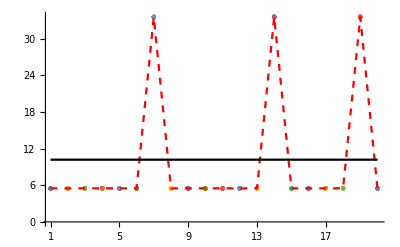

```mathematica
Which[NumericQ[forward[[1]]], 
Show[ListPlot[spot, Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle-> Red], ListPlot[strike & /@ forward, PlotStyle-> Black]]
, Head[forward[[1]]]==fd, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[spot[[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}]]
,True, "Check fc !"]
```

```mathematica
Max[Exp[-exerciseDates ir](Max[#-strike, 0] & /@ forward[[All, 1]])]
```

23.389

LS

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[23.3783,<|vol1→3.97710810338799×10^-23731,fc1→4.25802076295543×10^-23733,vol2→-1.1110509965764×10^-23714,fc2→5.5015696213438×10^-23717,vol3→-6.39804953242749×10^-23742,fc3→-5.48992659301822×10^-23745,vol4→-7.94068959583567×10^-23720,fc4→-3.0507362615564×10^-23722,vol5→-7.62065153972229×10^-23694,fc5→-1.78159547390746×10^-23696,vol6→-1.25493485237121×10^-23715,fc6→1.3981226804159×10^-23718,vol7→-2.5958821029272×10^-525,fc7→-6.83065010250599×10^-526,vol8→1.73492270054506×10^-23751,fc8→1.45500035625526×10^-23753,vol9→5.47932481029236×10^-23744,fc9→-2.23639538410164×10^-23747,vol10→1.14982952350132×10^-23760,fc10→7.43049996202034×10^-23764,vol11→2.8113491477991×10^-23762,fc11→4.89359271735006×10^-23765,vol12→3.64175001806537×10^-23763,fc12→2.51791692928633×10^-23766,vol13→-1.27890500065522×10^-23767,fc13→-1.09184930649659×10^-23770,vol14→1.11201,fc14→0.49561,vol15→1.05333486914978×10^-23709,fc15→-2.45986450352283×10^-23712,vol16→3.81427216427491×10^-23757,fc16→-1.28210713862218×10^-23759,vol17→-2.47223706745977×10^-23771,fc17→4.16527358309131×10^-23773,vol18→-4.09855119106082×10^-23755,fc18→-1.16493024272569×10^-23758,vol19→0.104666,fc19→0.503512,vol20→0.,fc20→0.|>]

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[23.3924,<|vol1→0,fc1→0,vol2→0.,fc2→0.,vol3→0.,fc3→0.,vol4→0.,fc4→0.,vol5→0.,fc5→0.,vol6→0.,fc6→0.,vol8→0.,fc8→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol12→0.,fc12→0.,vol13→0.,fc13→0.,vol15→0.,fc15→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol18→0.,fc18→0.,vol20→0.,fc20→0.,vol19→0.0863416,fc19→0.1748,vol14→0.47975,fc14→0.0999771,vol7→0.807372,fc7→0.724816|>]

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[23.3875,<|vol1→-3.73283445436365×10^-23755,fc1→-2.23280028296385×10^-23757,vol2→5.95018480251504×10^-23757,fc2→3.2071718712007×10^-23759,vol3→9.12544882446305×10^-23760,fc3→8.00252496762464×10^-23763,vol4→6.92685413759762×10^-23762,fc4→-1.47794294486298×10^-23764,vol5→-7.0025546644164×10^-23753,fc5→-5.32882143005644×10^-23755,vol6→-1.69326289059481×10^-23758,fc6→-3.09359966395385×10^-23761,vol7→0.677813,fc7→0.567004,vol8→2.99434348851702×10^-23755,fc8→8.81514791632059×10^-23758,vol9→-3.28492413357603×10^-23765,fc9→2.15548850155581×10^-23766,vol10→9.34274311202307×10^-23770,fc10→1.27847448734045×10^-23770,vol11→-4.43784511222072×10^-23776,fc11→-1.72179804355511×10^-23779,vol12→3.59530034535991×10^-23763,fc12→1.68917091058088×10^-23766,vol13→4.14291955940206×10^-23778,fc13→7.65498809678789×10^-23782,vol14→0.901685,fc14→0.261085,vol15→-2.01059645244703×10^-23770,fc15→1.32575923384318×10^-23773,vol16→9.67318811884508×10^-23764,fc16→1.0951799218265×10^-23766,vol17→-3.78417558124342×10^-23776,fc17→-2.66587015275978×10^-23778,vol18→-5.30043345028409×10^-23727,fc18→4.14657489185665×10^-23730,vol19→-0.0661695,fc19→0.17145,vol20→0.,fc20→0.|>]

Simple

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[22.5883,<|vol1→-0.000272944,fc1→-5.18553×10^-6,vol2→0.000105701,fc2→-6.78415×10^-7,vol3→-0.000015035,fc3→-1.52714×10^-7,vol4→-4.24248×10^-6,fc4→-1.41247×10^-7,vol5→-5.55529×10^-7,fc5→3.18502×10^-8,vol6→-7.39544×10^-7,fc6→-2.51478×10^-8,vol7→1.12935×10^-6,fc7→3.83679×10^-9,vol8→-7.22141×10^-8,fc8→-1.0404×10^-9,vol9→0.0510642,fc9→-0.00937263,vol10→-0.303719,fc10→0.00347498,vol11→0.0688639,fc11→0.0161802,vol12→0.0649962,fc12→0.00643082,vol13→1.65127×10^-8,fc13→-8.1758×10^-11,vol14→3.87315×10^-8,fc14→2.54247×10^-9,vol15→-1.36636×10^-8,fc15→-1.85138×10^-9,vol16→-1.54414×10^-8,fc16→2.50031×10^-10,vol17→3.7633×10^-9,fc17→1.87082×10^-10,vol18→-3.61428×10^-8,fc18→-9.76268×10^-10,vol19→0.104696,fc19→0.0342817,vol20→-0.445762,fc20→0.00403802|>]

LS

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 4.25802076295543×10^-23733 | 0. | 3.97710810338799×10^-23731 | 0.
2 | 5.5015696213438×10^-23717 | 0. | -1.1110509965764×10^-23714 | 0.
3 | -5.48992659301822×10^-23745 | 0. | -6.39804953242749×10^-23742 | 0.
4 | -3.0507362615564×10^-23722 | 0. | -7.94068959583567×10^-23720 | 0.
5 | -1.78159547390746×10^-23696 | 0. | -7.62065153972229×10^-23694 | 0.
6 | 1.3981226804159×10^-23718 | 0. | -1.25493485237121×10^-23715 | 0.
7 | -6.83065010250599×10^-526 | 0. | -2.5958821029272×10^-525 | 0.
8 | 1.45500035625526×10^-23753 | 0. | 1.73492270054506×10^-23751 | 0.
9 | -2.23639538410164×10^-23747 | 0. | 5.47932481029236×10^-23744 | 0.
10 | 7.43049996202034×10^-23764 | 0. | 1.14982952350132×10^-23760 | 0.
11 | 4.89359271735006×10^-23765 | 0. | 2.8113491477991×10^-23762 | 0.
12 | 2.51791692928633×10^-23766 | 0. | 3.64175001806537×10^-23763 | 0.
13 | -1.09184930649659×10^-23770 | 0. | -1.27890500065522×10^-23767 | 0.
14 | 0.49561 | 0.499403 | 1.11201 | 0.363134
15 | -2.45986450352283×10^-23712 | 0. | 1.05333486914978×10^-23709 | 0.
16 | -1.28210713862218×10^-23759 | 0. | 3.81427216427491×10^-23757 | 0.
17 | 4.16527358309131×10^-23773 | 0. | -2.47223706745977×10^-23771 | 0.
18 | -1.16493024272569×10^-23758 | 0. | -4.09855119106082×10^-23755 | 0.
19 | 0.503512 | 0.499635 | 0.104666 | 0.216261
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -5.4274052493569×10^-237555 | 0. | -5.256195619327×10^-237553 | 0.
2 | 2.71603986611136×10^-237422 | 0. | -6.73653770533679×10^-237420 | 0.
3 | -4.83706703110075×10^-237614 | 0. | -7.35990951975728×10^-237611 | 0.
4 | -7.58213051012076×10^-237418 | 0. | -6.27659671792355×10^-237415 | 0.
5 | -4.56520217250309×10^-237300 | 0. | -3.04827191883303×10^-237297 | 0.
6 | 7.97303705523596×10^-237460 | 0. | -6.40376898138697×10^-237457 | 0.
7 | 0.663505 | 0.577583 | 0.845256 | 0.303763
8 | 2.95958645456065×10^-237562 | 0. | 2.56082786824763×10^-237560 | 0.
9 | -3.66004672303036×10^-237584 | 0. | 1.89200691538697×10^-237580 | 0.
10 | 1.73010120760707×10^-237650 | 0. | 5.225484640225×10^-237647 | 0.
11 | 2.32944399883744×10^-237658 | 0. | 1.73164372361056×10^-237655 | 0.
12 | 2.18298828419514×10^-237647 | 0. | 2.05300679535724×10^-237644 | 0.
13 | 1.4114240393551×10^-237628 | 0. | 3.9042377710925×10^-237625 | 0.
14 | 0.142591 | 0.197573 | 0.713608 | 0.555466
15 | -4.51641456630404×10^-237078 | 0. | 1.93396706990128×10^-237075 | 0.
16 | -9.17322142159098×10^-237557 | 0. | 2.71811895314064×10^-237554 | 0.
17 | 2.77983631048129×10^-237698 | 0. | -1.48443891470433×10^-237696 | 0.
18 | -2.80648334473347×10^-237526 | 0. | -7.98256542319315×10^-237523 | 0.
19 | 0.193472 | 0.224279 | -0.113659 | -0.0289138
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -2.49255438036029×10^-237479 | 0. | -8.75817294407484×10^-237476 | 0.
2 | 4.58380913483279×10^-237484 | 0. | 1.38057771155252×10^-237482 | 0.
3 | -2.19163478547698×10^-237642 | 0. | 1.29008666397279×10^-237640 | 0.
4 | 3.82509529827915×10^-237601 | 0. | -2.86279956942715×10^-237598 | 0.
5 | -1.34270775768941×10^-237348 | 0. | 1.27017100184539×10^-237344 | 0.
6 | -3.27169018971721×10^-237730 | 0. | -9.18225507175832×10^-237728 | 0.
7 | 0.587176 | 0.551926 | 1.6784 | 1.02876
8 | -7.52441291831715×10^-237705 | 0. | 3.66477031228861×10^-237702 | 0.
9 | 4.60853999628934×10^-237704 | 0. | -6.94535192333214×10^-237701 | 0.
10 | -4.33303627205417×10^-237790 | 0. | -8.12815237423811×10^-237788 | 0.
11 | 2.27403110126384×10^-237753 | 0. | -2.18267823455118×10^-237751 | 0.
12 | 3.67344976788068×10^-237809 | 0. | 2.92796148188805×10^-237806 | 0.
13 | -1.05814661166837×10^-237766 | 0. | -9.82929486101079×10^-237764 | 0.
14 | 0.279336 | 0.279207 | 0.968931 | 0.898799
15 | 2.05325862584566×10^-237384 | 0. | 2.03168043401288×10^-237381 | 0.
16 | -3.22048823997539×10^-237366 | 0. | -3.53719497385504×10^-237363 | 0.
17 | 5.6392298030645×10^-237678 | 0. | 2.45482748736571×10^-237675 | 0.
18 | 5.7836653716537×10^-237398 | 0. | 3.2288723143041×10^-237395 | 0.
19 | 0.13318 | 0.168439 | -0.161161 | -0.128084
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 6.6881400720423×10^-237643 | 0. | 1.1018752438468×10^-237640 | 0.
2 | 1.71138063638962×10^-237595 | 0. | 3.14223259382026×10^-237593 | 0.
3 | 1.76928332997489×10^-237676 | 0. | 1.88561688486753×10^-237673 | 0.
4 | -5.03094703358281×10^-237645 | 0. | 1.96391599779536×10^-237642 | 0.
5 | -8.3366715595266×10^-237461 | 0. | -1.03072498142147×10^-237458 | 0.
6 | -6.50606416077727×10^-237638 | 0. | -4.25832147402225×10^-237635 | 0.
7 | 0.556637 | 0.52825 | 1.57472 | 0.925786
8 | 2.1729440128927×10^-237572 | 0. | 7.05475393416936×10^-237570 | 0.
9 | 3.88566779789639×10^-237722 | 0. | -4.97037695548022×10^-237721 | 0.
10 | 1.42545800707801×10^-237796 | 0. | 1.87104708870919×10^-237796 | 0.
11 | 4.83315218909113×10^-237817 | 0. | 2.23684924625657×10^-237814 | 0.
12 | 3.61760831676207×10^-237740 | 0. | 8.15280859578532×10^-237737 | 0.
13 | 1.03798608213576×10^-237873 | 0. | 5.54832882725053×10^-237870 | 0.
14 | 0.310752 | 0.29279 | 1.34628 | 1.16934
15 | 4.42283015206491×10^-237688 | 0. | -5.38423424146026×10^-237685 | 0.
16 | -8.56337345667078×10^-237596 | 0. | -7.70500408190424×10^-237593 | 0.
17 | -1.13507241576207×10^-237737 | 0. | -1.59315051212782×10^-237735 | 0.
18 | 7.35134695407992×10^-237240 | 0. | -9.3969906046005×10^-237237 | 0.
19 | 0.132313 | 0.178532 | -0.254851 | -0.187108
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -1.64107103215699×10^-118811 | 0. | -2.8946453515351×10^-118809 | 0.
2 | 4.30085451851616×10^-118795 | 0. | 8.31991820636702×10^-118793 | 0.
3 | 3.43046198306886×10^-118828 | 0. | 3.77471607583637×10^-118825 | 0.
4 | -5.27667053716515×10^-118817 | 0. | 2.18382348344775×10^-118814 | 0.
5 | -2.45035579445484×10^-118741 | 0. | -3.12309368915709×10^-118739 | 0.
6 | -5.5092689976191×10^-118805 | 0. | -3.42504078338798×10^-118802 | 0.
7 | 0.566256 | 0.534108 | 1.3615 | 0.69079
8 | 1.98691582427737×10^-118781 | 0. | 6.46682624673776×10^-118779 | 0.
9 | 1.08226774012856×10^-118850 | 0. | -1.43464503929738×10^-118849 | 0.
10 | 5.15808751490936×10^-118885 | 0. | 9.81031111404628×10^-118885 | 0.
11 | 1.94280403812081×10^-118901 | 0. | 7.79589250457644×10^-118899 | 0.
12 | 2.55077405401992×10^-118848 | 0. | 5.77230900808142×10^-118845 | 0.
13 | 5.25070877249206×10^-118924 | 0. | 2.77938696422228×10^-118920 | 0.
14 | 0.292617 | 0.280244 | 1.27392 | 0.993785
15 | 1.3988997105502×10^-118846 | 0. | -1.72670447091896×10^-118843 | 0.
16 | -8.89943459442655×10^-118802 | 0. | -8.01138080133443×10^-118799 | 0.
17 | -2.60786645090491×10^-118871 | 0. | -3.67084637981202×10^-118869 | 0.
18 | 3.12141238379129×10^-118623 | 0. | -3.99000115581424×10^-118620 | 0.
19 | 0.140801 | 0.185175 | -0.188429 | -0.120627
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -2.23280028296385×10^-23757 | 0. | -3.73283445436365×10^-23755 | 0.
2 | 3.2071718712007×10^-23759 | 0. | 5.95018480251504×10^-23757 | 0.
3 | 8.00252496762464×10^-23763 | 0. | 9.12544882446305×10^-23760 | 0.
4 | -1.47794294486298×10^-23764 | 0. | 6.92685413759762×10^-23762 | 0.
5 | -5.32882143005644×10^-23755 | 0. | -7.0025546644164×10^-23753 | 0.
6 | -3.09359966395385×10^-23761 | 0. | -1.69326289059481×10^-23758 | 0.
7 | 0.567004 | 0.534172 | 0.677813 | 0.220685
8 | 8.81514791632059×10^-23758 | 0. | 2.99434348851702×10^-23755 | 0.
9 | 2.15548850155581×10^-23766 | 0. | -3.28492413357603×10^-23765 | 0.
10 | 1.27847448734045×10^-23770 | 0. | 9.34274311202307×10^-23770 | 0.
11 | -1.72179804355511×10^-23779 | 0. | -4.43784511222072×10^-23776 | 0.
12 | 1.68917091058088×10^-23766 | 0. | 3.59530034535991×10^-23763 | 0.
13 | 7.65498809678789×10^-23782 | 0. | 4.14291955940206×10^-23778 | 0.
14 | 0.261085 | 0.25806 | 0.901685 | 0.608542
15 | 1.32575923384318×10^-23773 | 0. | -2.01059645244703×10^-23770 | 0.
16 | 1.0951799218265×10^-23766 | 0. | 9.67318811884508×10^-23764 | 0.
17 | -2.66587015275978×10^-23778 | 0. | -3.78417558124342×10^-23776 | 0.
18 | 4.14657489185665×10^-23730 | 0. | -5.30043345028409×10^-23727 | 0.
19 | 0.17145 | 0.207185 | -0.0661695 | -0.0223701
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 0 | 0. | 0 | 0.
2 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0.
5 | 0. | 0. | 0. | 0.
6 | 0. | 0. | 0. | 0.
7 | 0.724816 | 0.724816 | 0.807372 | 0.807372
8 | 0. | 0. | 0. | 0.
9 | 0. | 0. | 0. | 0.
10 | 0. | 0. | 0. | 0.
11 | 0. | 0. | 0. | 0.
12 | 0. | 0. | 0. | 0.
13 | 0. | 0. | 0. | 0.
14 | 0.0999771 | 0.0999771 | 0.47975 | 0.47975
15 | 0. | 0. | 0. | 0.
16 | 0. | 0. | 0. | 0.
17 | 0. | 0. | 0. | 0.
18 | 0. | 0. | 0. | 0.
19 | 0.1748 | 0.1748 | 0.0863416 | 0.0863416
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0.
5 | 0. | 0. | 0. | 0.
6 | 0. | 0. | 0. | 0.
7 | 0.724816 | 0.724816 | 0.807372 | 0.807372
8 | 0. | 0. | 0. | 0.
9 | 0. | 0. | 0. | 0.
10 | 0. | 0. | 0. | 0.
11 | 0. | 0. | 0. | 0.
12 | 0. | 0. | 0. | 0.
13 | 0. | 0. | 0. | 0.
14 | 0.0999771 | 0.0999771 | 0.47975 | 0.47975
15 | 0. | 0. | 0. | 0.
16 | 0. | 0. | 0. | 0.
17 | 0. | 0. | 0. | 0.
18 | 0. | 0. | 0. | 0.
19 | 0.1748 | 0.1748 | 0.0863416 | 0.0863416
20 | 0. | 0. | 0. | 0.

1k sims

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]]},
TableForm[Transpose[{Range[Length[vs]], fcbar,volbar}], TableHeadings->{None, {"day","delta_manual", "vega_manual" }}]
]
```

day | delta_manual | vega_manual
1 | 0. | 0.
2 | 0. | 0.
3 | 0.0130472 | 0.000897061
4 | 0.169472 | 0.00729841
5 | 0.289231 | 0.00738155
6 | 0.17273 | 0.00301251
7 | 0.0581684 | 0.000698378
8 | 0.00690373 | -0.000119574
9 | 0.000696961 | 0.0000494829
10 | 0. | 0.
11 | 0. | 0.
12 | 0. | 0.
13 | 0. | 0.
14 | 0. | 0.
15 | 0. | 0.
16 | 0. | 0.
17 | 0. | 0.
18 | 0. | 0.
19 | 0. | 0.
20 | 0. | 0.

10k sims

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]]},
TableForm[Transpose[{Range[Length[vs]], fcbar,volbar}], TableHeadings->{None, {"day","delta_manual", "vega_manual" }}]
]
```

day | delta_manual | vega_manual
1 | 0. | 0.
2 | 0. | 0.
3 | 0.0134607 | 0.000907438
4 | 0.170779 | 0.00741076
5 | 0.281584 | 0.00781044
6 | 0.187397 | 0.00341653
7 | 0.0518907 | 0.000583088
8 | 0.00658878 | 0.0000506197
9 | 0.000807085 | 0.0000101221
10 | 0.0000590161 | 2.66501×10^-6
11 | 0. | 0.
12 | 0. | 0.
13 | 0. | 0.
14 | 0. | 0.
15 | 0. | 0.
16 | 0. | 0.
17 | 0. | 0.
18 | 0. | 0.
19 | 0. | 0.
20 | 0.0000428829 | -1.96197×10^-6

Simple

### Bermudan: Value and sensitivities (automatic and manual, both loops)

#### Inputs

```mathematica
elapsedStart=Date[];
SeedRandom[123];
nE=30;
nMC=10^2;
nB=5;
exerciseDates=Range[1, nE, 1]/365.242;
rvsBkwd=RandomVariate[NormalDistribution[0, 1] ,{nMC  / 2, nE}];
rvsBkwd=Join[rvsBkwd, -rvsBkwd];
rvsFwd=RandomVariate[NormalDistribution[0, 1] ,{nMC / 2, nE}]; (* rvsBkwd;*)
rvsFwd = Join[rvsFwd,-rvsFwd];
(*forward=23.0+10 Sin[2 π Range[nE]/(nE / 1)];*)
forward = ConstantArray[25.5, nE];
forward[[7]]=33.6; (*30.1;*)
(*forward[[14]]=33.6;*)
forward[[19]]=33.6;
(*forward=Join[23.0+2 Sin[2 π Range[nE/2]/(nE / 1)], ConstantArray[23.0+Sin[2 π nE/2/(nE / 1)], nE / 2]];*)
forward=MapThread[fd[#1, <|#2->1|>]&,{forward, "fc"<>ToString[#] & /@ Range[nE]}];
sigma = 0.45;
(*tv=Sqrt[Range[nE]/365.242 fd[0.45, <|Unique["vol"]->1|>]^2];*)
(*tv=Sqrt[Range[nE]/365.242]  (fd[sigma, <|Unique["vol"]->1|>] & /@ Range[nE]);*)
(*tv=Sqrt[exerciseDates] MapThread[fd[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];*)

vols = MapThread[fd[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];
(*vols = sigma & /@ Range[nE];*)

(*spot=simulationSpot[forward, tv, rvs ];*)

ir =  ConstantArray[0.0245, nE];

(*irt = 0.0245 exerciseDates & /@ Range[nMC];*)
(*numeraire=Exp[irt];*)

(*strike=RandomReal[MinMax[Flatten[spot[[All, All, 1]]]]];*)
(*strike=Mean[Flatten[spot[[All, All, 1]]]];*)
strike = 25.5;(*10.2;*) (*forward[[-1, 1]]*); (*20.2*) ; (*forward[[3, 1]];*)

(*exerciseValue=Map[payoffBermudean[#, strike] &,spot, {2}];*)

(*basisFunctions = Function[x,Evaluate@Table[LaguerreL[n,x], {n,nB}]];*)
basisFunctions = Function[x, {x/x, x, x^2, x^3, x^4}[[1;;5]]]; (*Function[x,Table[LaguerreL[n,x],{n,5}]]*)

(*phi = basisFunctions[spot];*)
elapsedEnd=Date[];
DateDifference[elapsedStart, elapsedEnd, "Minute"]

(*forward=(23.0+10 Sin[2 π Range[nE]/(nE / 1)])/100;
vols = sigma & /@ Range[nE];*)
```

0.000550055 min

```mathematica
{elapsed, output} = regressionCoefficientAndSensitivityBothLoopsNew[exerciseDates,forward,vols,ir,rvsBkwd,rvsFwd,strike,basisFunctions]//AbsoluteTiming;
```

```mathematica
elapsed
```

1750.26

```mathematica
elapsed
```

5315.95

```mathematica
output["elapsedBkwd"]
output["elapsedFwd"]
```

19.9944

9.17346

```mathematica
output["elapsedBkwd"]
output["elapsedFwd"]
```

41.3828

47.2127

```mathematica
Keys[output]
```

{fcBarBkwd,volBarBkwd,outBetaBkwd,outHoldValueBkwd,outValueBkwd,outBetaFwd,outHoldValueFwd,outValueFwd,outCashflowFwd,fcBarFwd,volBarFwd,spotBkwd,spotFwd,elapsedBkwd,elapsedFwd,notExercised}

```mathematica
output["notExercised"]//Dimensions
```

{30,100}

```mathematica
actions=With[{local=(PositionIndex[#][1][[-1]]& /@  Transpose[output["notExercised"]])},
{#, Count[local,#]}& /@ Range[nE]
]
```

{{1,100},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0}}

```mathematica
TableForm[ N@#[[2]]/nMC & /@ actions, TableHeadings->{Range[nE]}]
```

1 | 0.
2 | 0.
3 | 0.
4 | 0.
5 | 0.01
6 | 0.
7 | 0.36
8 | 0.
9 | 0.
10 | 0.
11 | 0.
12 | 0.
13 | 0.
14 | 0.
15 | 0.
16 | 0.
17 | 0.
18 | 0.01
19 | 0.54
20 | 0.
21 | 0.
22 | 0.
23 | 0.03
24 | 0.01
25 | 0.
26 | 0.
27 | 0.
28 | 0.
29 | 0.01
30 | 0.03

```mathematica
TableForm[ N@#[[2]]/nMC & /@ actions, TableHeadings->{Range[nE]}]
```

1 | 1.
2 | 0.
3 | 0.
4 | 0.
5 | 0.
6 | 0.
7 | 0.
8 | 0.
9 | 0.
10 | 0.
11 | 0.
12 | 0.
13 | 0.
14 | 0.
15 | 0.
16 | 0.
17 | 0.
18 | 0.
19 | 0.
20 | 0.
21 | 0.
22 | 0.
23 | 0.
24 | 0.
25 | 0.
26 | 0.
27 | 0.
28 | 0.
29 | 0.
30 | 0.

```mathematica
TableForm[output["notExercised"][[All, 1;;20]], TableHeadings->{Range[nE], Range[nMC]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
7 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
8 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
9 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
10 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
11 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
12 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
13 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
14 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
15 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
16 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
17 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
18 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
19 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
20 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
21 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
22 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
23 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
24 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
25 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
26 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
27 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
28 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
29 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
30 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
output["outBetaBkwd"][[All, All, 1]]
```

{{533992.,-84107.5,4966.5,-130.305,1.28167},{811.802,-340.98,32.653,-1.18033,0.0147363},{-11096.8,1642.11,-90.4686,2.1995,-0.0198951},{30878.4,-4780.09,277.371,-7.14799,0.0690254},{-19326.9,3066.46,-181.913,4.78375,-0.0470452},{-1642.36,218.918,-10.5756,0.218267,-0.00159293},{5166.73,-567.707,23.1817,-0.415908,0.00276333},{-1032.34,155.006,-8.61231,0.211152,-0.00192295},{3040.77,-513.904,32.3412,-0.896811,0.00925384},{3801.33,-621.487,38.0852,-1.03394,0.0104868},{685.966,-99.1344,5.38575,-0.128675,0.00113957},{-133.798,6.02879,0.567865,-0.0376409,0.000576035},{-591.84,92.1464,-5.2772,0.133367,-0.00125251},{-2606.23,409.091,-23.9133,0.618704,-0.00597596},{-619.998,98.3041,-5.70687,0.145723,-0.00138119},{1954.1,-283.361,15.2347,-0.358316,0.00311012},{762.216,-108.827,5.79695,-0.13483,0.00115293},{-179.254,42.1093,-3.13521,0.0971758,-0.00108589},{90.4,-17.0481,1.06083,-0.026756,0.000238415},{-3101.53,484.541,-28.097,0.717781,-0.00681766},{39.1004,-10.131,0.844041,-0.0278882,0.0003238},{-63.2332,11.8736,-0.772646,0.0217669,-0.000223375},{561.781,-86.1677,4.95228,-0.125657,0.00118837},{-1839.98,293.177,-17.3592,0.453517,-0.00441084},{1384.71,-226.002,13.7412,-0.368069,0.00366518},{221.658,-31.628,1.67844,-0.0387037,0.000326713},{31.9518,-2.96531,0.0689557,0.00102645,-0.000037097},{1215.16,-182.665,10.2756,-0.256087,0.00238658},{257.33,-39.3927,2.24443,-0.0560262,0.000515563}}

```mathematica
output["outBetaFwd"][[All, All, 1]]
```

{{-44768.,7098.05,-421.816,11.1371,-0.110227},{4765.01,-738.994,43.0051,-1.11073,0.0107405},{1016.16,-183.656,12.2799,-0.358428,0.00386487},{-17828.1,2756.48,-159.4,4.08781,-0.0392262},{701.153,-105.18,5.96948,-0.150025,0.00140849},{1620.42,-232.425,12.4614,-0.293974,0.00256983},{340.031,-42.3127,2.00527,-0.0418703,0.000325168},{-4276.77,651.248,-37.0156,0.932634,-0.00879017},{1529.17,-238.519,13.9361,-0.359464,0.00345335},{-17.0342,3.57016,-0.185616,0.00421413,-0.0000351311},{-10.7874,1.0477,0.0579324,-0.00467234,0.0000764006},{258.148,-32.182,1.47963,-0.0279538,0.000170763},{26.1222,-1.81746,0.0478784,0.000266993,-0.0000166542},{67.4843,-9.0235,0.509784,-0.012639,0.000115972},{1301.34,-195.216,10.989,-0.273286,0.00253275},{11.2607,-0.195184,-0.00594814,0.000642741,-0.0000111744},{763.237,-113.454,6.33965,-0.156109,0.00142934},{-366.29,56.8176,-3.19059,0.0787116,-0.000720861},{48.268,-4.2524,0.144199,-0.00197594,8.48701×10^-6},{-51.6527,7.9476,-0.416451,0.00947864,-0.0000789107},{-446.114,71.329,-4.21507,0.109956,-0.0010677},{169.778,-26.6876,1.57029,-0.040119,0.000375841},{-277.912,42.1085,-2.32192,0.056005,-0.00049909},{-347.846,56.0061,-3.2832,0.0838259,-0.000785778},{103.153,-18.3486,1.21037,-0.0342201,0.000351567},{-23.0922,4.37083,-0.27911,0.0078805,-0.0000818793},{-1625.44,259.63,-15.3502,0.398926,-0.00384558},{154.861,-23.8968,1.36909,-0.0341055,0.00031218},{-150.525,24.747,-1.4943,0.0396127,-0.000389035}}

```mathematica
output["outValueFwd"][[1]]//Mean
```

fd[8.61268,<|vol1→0.76364,fc1→0.0170785|>]

```mathematica
output["outValueFwd"][[1]]//Mean
```

fd[8.58232,<|vol1→0.818426,fc1→0.0434779|>]

```mathematica
output["outValueBkwd"][[1]]//Mean
```

fd[8.66097,<|vol1→0.,fc1→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.,vol4→0.,fc4→0.,vol5→0.,fc5→0.,vol6→0.,fc6→0.,vol7→1.57083,fc7→0.340757,vol8→0.,fc8→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol12→0.,fc12→0.,vol13→0.,fc13→0.,vol14→0.,fc14→0.,vol15→0.,fc15→0.,vol16→0.,fc16→0.,vol17→0.332708,fc17→0.025313,vol18→0.321473,fc18→0.0251474,vol19→0.779304,fc19→0.521,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.240736,fc22→0.0239809,vol23→0.217013,fc23→0.0236336,vol24→0.0985732,fc24→0.0116673,vol25→0.209123,fc25→0.0235109,vol26→0.0717504,fc26→0.011253,vol27→0.291421,fc27→0.0246999,vol29→0.,fc29→0.,vol30→0.139383,fc30→0.0122932,vol28→0.0902634,fc28→0.0216547|>]

```mathematica
output["outValueBkwd"][[1]]//Mean
```

fd[8.63499,<|vol1→-2.71784578021398×10^-1216,fc1→-1.53659738959405×10^-1216,vol2→-5.10598174437092×10^-991,fc2→-1.54667995794716×10^-991,vol3→2.04274712179074×10^-618,fc3→9.44907557983748×10^-623,vol4→-8.25703539123763×10^-826,fc4→-1.75186288690648×10^-826,vol5→-5.47240310255813×10^-669,fc5→-8.20012137311845×10^-670,vol6→8.72136817209346×10^-479,fc6→-5.6060631849088×10^-485,vol7→0.889553,fc7→-0.107642,vol8→6.47111765757964×10^-475,fc8→1.26536032418596×10^-482,vol9→-1.9353546170358×10^-668,fc9→-2.66465701647879×10^-669,vol10→-1.60319035671105×10^-462,fc10→-2.40006367061511×10^-463,vol11→1.59575×10^-67,fc11→1.43115×10^-68,vol12→-1.61476676893972×10^-322,fc12→-1.58666380179572×10^-323,vol13→-1.62386×10^-78,fc13→-1.06062×10^-79,vol14→-1.03638217399662×10^-476,fc14→-1.07096584756509×10^-477,vol15→-2.50052×10^-48,fc15→-1.79222×10^-49,vol16→-0.0320758,fc16→-0.00269392,vol17→0.60043,fc17→0.045686,vol18→0.521816,fc18→0.0412766,vol19→1.77481,fc19→0.926509,vol20→-0.00229903,fc20→-0.000152118,vol21→-0.0189829,fc21→-0.00185251,vol22→0.0616463,fc22→0.00415787,vol23→0.21774,fc23→0.0217235,vol24→-0.182262,fc24→-0.025491,vol25→0.564341,fc25→0.05367,vol26→-0.115039,fc26→-0.0279578,vol27→0.387806,fc27→0.0380329,vol28→0.725288,fc28→0.174864,vol30→-0.0295981,fc30→-0.00721003,vol29→-0.110405,fc29→-0.0205314|>]

```mathematica
output["outCashflowFwd"]//Mean
```

fd[8.87672,<|vol1→0.,fc1→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.,vol4→0.,fc4→0.,vol5→0.0983456,fc5→0.0116227,vol6→0.,fc6→0.,vol7→1.70343,fc7→0.382463,vol8→0.,fc8→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol12→0.,fc12→0.,vol13→0.,fc13→0.,vol14→0.,fc14→0.,vol15→0.,fc15→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol18→0.177591,fc18→0.0128181,vol19→1.0045,fc19→0.553583,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.329866,fc23→0.0354985,vol24→0.104592,fc24→0.0117587,vol25→0.,fc25→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol28→0.,fc28→0.,vol29→0.0341351,fc29→0.0106468,vol30→0.0743158,fc30→0.0213898|>]

```mathematica
output["outCashflowFwd"]//Mean
```

fd[8.97845,<|vol29→0.0352034,fc29→0.0107183,vol27→0.0867804,fc27→0.0174488,vol7→1.71713,fc7→0.426536,vol1→0.,fc1→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.,vol4→0.,fc4→0.,vol5→-23.557,fc5→-2.78401,vol6→0.,fc6→0.,vol8→0.,fc8→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→-1.4785×10^-205,fc11→-1.54925×10^-206,vol12→0.,fc12→0.,vol13→0.,fc13→0.,vol14→-3.65102×10^-197,fc14→-3.56061×10^-198,vol15→-8.29614×10^-246,fc15→-7.71783×10^-247,vol16→-7.63578×10^-31,fc16→-6.39581×10^-32,vol17→-1.11398×10^-64,fc17→-1.01012×10^-65,vol18→0.0951565,fc18→0.00686821,vol19→-1.01919,fc19→0.807629,vol20→3.94498×10^-6,fc20→4.25919×10^-7,vol21→-0.00202302,fc21→-0.000279199,vol22→0.0113829,fc22→0.000974134,vol23→0.316386,fc23→0.0338264,vol24→0.0741263,fc24→0.00833363,vol25→-0.0102441,fc25→-0.00212594,vol26→0.0436578,fc26→0.00709582,vol28→-3.61538×10^-8,fc28→-1.12068×10^-8,vol30→0.0254436,fc30→0.0114457|>]

```mathematica
Mean[Log[output["spotBkwd"]]]-Log[forward]-(-1/2 vols^2 exerciseDates)
```

{fd[0.,<|fc1→0.,vol1→-1.51788×10^-18|>],fd[4.44089×10^-16,<|fc2→0.,vol2→-3.03577×10^-18|>],fd[0.,<|fc3→0.,vol3→4.33681×10^-19|>],fd[4.44089×10^-16,<|fc4→6.93889×10^-18,vol4→3.46945×10^-18|>],fd[-4.44089×10^-16,<|fc5→0.,vol5→-2.60209×10^-18|>],fd[0.,<|fc6→6.93889×10^-18,vol6→-7.80626×10^-18|>],fd[0.,<|fc7→3.46945×10^-18,vol7→-5.20417×10^-18|>],fd[0.,<|fc8→0.,vol8→-3.46945×10^-18|>],fd[0.,<|fc9→0.,vol9→1.73472×10^-18|>],fd[0.,<|fc10→0.,vol10→3.46945×10^-18|>],fd[0.,<|fc11→0.,vol11→6.93889×10^-18|>],fd[4.44089×10^-16,<|fc12→0.,vol12→-1.56125×10^-17|>],fd[0.,<|fc13→0.,vol13→1.38778×10^-17|>],fd[4.44089×10^-16,<|fc14→0.,vol14→6.93889×10^-18|>],fd[4.44089×10^-16,<|fc15→0.,vol15→-1.04083×10^-17|>],fd[4.44089×10^-16,<|fc16→0.,vol16→-6.93889×10^-18|>],fd[-4.44089×10^-16,<|fc17→0.,vol17→0.|>],fd[0.,<|fc18→0.,vol18→3.46945×10^-18|>],fd[-4.44089×10^-16,<|fc19→0.,vol19→6.93889×10^-18|>],fd[8.88178×10^-16,<|fc20→0.,vol20→-1.04083×10^-17|>],fd[0.,<|fc21→0.,vol21→1.04083×10^-17|>],fd[0.,<|fc22→6.93889×10^-18,vol22→-3.46945×10^-18|>],fd[0.,<|fc23→0.,vol23→-3.46945×10^-18|>],fd[4.44089×10^-16,<|fc24→0.,vol24→3.46945×10^-18|>],fd[0.,<|fc25→0.,vol25→-1.04083×10^-17|>],fd[4.44089×10^-16,<|fc26→0.,vol26→-6.93889×10^-18|>],fd[0.,<|fc27→0.,vol27→-6.93889×10^-18|>],fd[4.44089×10^-16,<|fc28→0.,vol28→0.|>],fd[4.44089×10^-16,<|fc29→6.93889×10^-18,vol29→2.08167×10^-17|>],fd[4.44089×10^-16,<|fc30→0.,vol30→6.93889×10^-18|>]}

```mathematica
stDev[(#-Log[forward]-(-1/2 vols^2 exerciseDates)) & /@ Log[output["spotBkwd"]]]/Sqrt[exerciseDates]
```

{19.1113 stDev[{{fd[0.0292339,<|fc1→6.93889×10^-18,vol1→0.0649641|>],fd[-0.00579762,<|fc2→0.,vol2→-0.0128836|>],fd[0.0135543,<|fc3→0.,vol3→0.0301207|>],fd[-0.00378709,<|fc4→0.,vol4→-0.00841575|>]},98,{fd[-0.0112737,<|fc1→0.,vol1→-0.0250527|>],fd[20,1],1,fd[0.0380529,<|fc4→0.,vol4→0.0845621|>]}}],2,1}
 |  |  |  |

```mathematica
Mean[Log[output["spotFwd"]]]-Log[forward]-(-1/2 vols^2 exerciseDates)
```

{-8.88178×10^-16,8.88178×10^-16,2.22045×10^-15,1.33227×10^-15,-4.44089×10^-16,-4.44089×10^-16,1.33227×10^-15,-1.33227×10^-15,-4.44089×10^-16,0.,0.,4.44089×10^-16,0.,1.33227×10^-15,-1.33227×10^-15,4.44089×10^-16,-8.88178×10^-16,1.33227×10^-15,-4.44089×10^-16,0.,1.33227×10^-15,-1.33227×10^-15,-1.33227×10^-15,0.,4.44089×10^-16,0.,1.33227×10^-15,-4.44089×10^-16,-8.88178×10^-16,8.88178×10^-16}

```mathematica
StandardDeviation[(#-Log[forward]-(-1/2 vols^2 exerciseDates)) & /@ Log[output["spotFwd"]]]/Sqrt[exerciseDates]
```

{0.419455,0.473607,0.430283,0.463635,0.503017,0.495062,0.441388,0.403061,0.426802,0.482642,0.380412,0.418701,0.4915,0.491245,0.41609,0.492069,0.403334,0.425701,0.474884,0.423677,0.429637,0.421335,0.490736,0.484552,0.377187,0.500114,0.460802,0.481769,0.455446,0.425729}

```mathematica
Mean[output["spotBkwd"]]
```

{fd[25.5004,<|vol1→0.00172627,fc1→1.00002|>],fd[25.4983,<|vol2→-0.00748704,fc2→0.999934|>],fd[25.5008,<|vol3→0.00366046,fc3→1.00003|>],fd[25.5011,<|vol4→0.00476034,fc4→1.00004|>]}

```mathematica
Mean[output["spotFwd"]]
```

{fd[25.4994,<|vol1→-0.00273009,fc1→0.999976|>],fd[25.5025,<|vol2→0.0112511,fc2→1.0001|>],fd[25.4948,<|vol3→-0.022994,fc3→0.999797|>],fd[25.5112,<|vol4→0.0497457,fc4→1.00044|>]}

```mathematica
Map[Chop,Total[output["outValueBkwd"][[1]]] / Length[output["outValueBkwd"][[1]]], Infinity]
```

fd[0.776587,<|vol1→0.198293,fc1→0.0834469,vol2→0.427619,fc2→0.157427,vol3→0.586373,fc3→0.220217,vol4→0.53063,fc4→0.249277|>]

```mathematica
Map[Chop,Total[output["outValueFwd"][[1]]] / Length[output["outValueFwd"][[1]]], Infinity]
```

fd[0.79332,<|vol1→0.187305,fc1→0.137856|>]

```mathematica
Map[Chop,Total[output["outCashflowFwd"] ]/ Length[output["outCashflowFwd"]], Infinity]
```

fd[0.854593,<|vol1→0.122358,fc1→0.0421095,vol2→0.661682,fc2→0.25149,vol3→0.477428,fc3→0.17832,vol4→0.660404,fc4→0.271455|>]

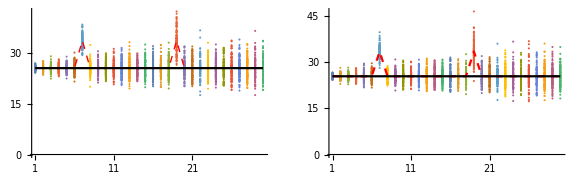

```mathematica
GraphicsRow[{Which[NumericQ[forward[[1]]], 
Show[ListPlot[output["spotBkwd"], Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle-> Red], ListPlot[strike & /@ forward, PlotStyle-> Black]]
, Head[forward[[1]]]==fd, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[output["spotBkwd"][[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed, Thick],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}]]
,True, "Check fc !"], Which[NumericQ[forward[[1]]], 
Show[ListPlot[output["spotFwd"], Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle-> Red], ListPlot[strike & /@ forward, PlotStyle-> Black]]
, Head[forward[[1]]]==fd, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[output["spotFwd"][[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}]]
,True, "Check fc !"]}, ImageSize->Large]
```

```mathematica
Keys[output]
```

{fcBarBkwd,volBarBkwd,outBetaBkwd,outHoldValueBkwd,outValueBkwd,outBetaFwd,outHoldValueFwd,outValueFwd,outCashflowFwd,fcBarFwd,volBarFwd,spotBkwd,spotFwd,elapsedBkwd,elapsedFwd,notExercised}

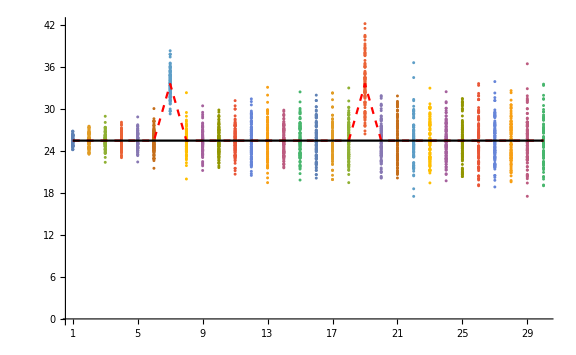

```mathematica
Which[NumericQ[forward[[1]]], 
Show[ListPlot[output["spotBkwd"], Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle-> Red], ListPlot[strike & /@ forward, PlotStyle-> Black], ImageSize->Large]
, Head[forward[[1]]]==fd, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[output["spotBkwd"][[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}], ImageSize->Large]
,True, "Check fc !"]
```

```mathematica
Max[Exp[-exerciseDates ir](Max[#-strike, 0] & /@ forward[[All, 1]])]
```

8.0962

### mod_payoff

Backward

```mathematica
Module[{res=Mean[output["outValueBkwd"][[1]]] ,fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, output["fcBarBkwd"][[All,1]],res[[2]][#] & /@ vol,  output["volBarBkwd"][[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_fd | delta_manual | vega_fd | vega_manual
1 | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0.
5 | 0. | 0. | 0. | 0.
6 | 0. | 0. | 0. | 0.
7 | 0.340757 | 0.340757 | 1.57083 | 1.57083
8 | 0. | 0. | 0. | 0.
9 | 0. | 0. | 0. | 0.
10 | 0. | 0. | 0. | 0.
11 | 0. | 0. | 0. | 0.
12 | 0. | 0. | 0. | 0.
13 | 0. | 0. | 0. | 0.
14 | 0. | 0. | 0. | 0.
15 | 0. | 0. | 0. | 0.
16 | 0. | 0. | 0. | 0.
17 | 0.025313 | 0.025313 | 0.332708 | 0.332708
18 | 0.0251474 | 0.0251474 | 0.321473 | 0.321473
19 | 0.521 | 0.521 | 0.779304 | 0.779304
20 | 0. | 0. | 0. | 0.
21 | 0. | 0. | 0. | 0.
22 | 0.0239809 | 0.0239809 | 0.240736 | 0.240736
23 | 0.0236336 | 0.0236336 | 0.217013 | 0.217013
24 | 0.0116673 | 0.0116673 | 0.0985732 | 0.0985732
25 | 0.0235109 | 0.0235109 | 0.209123 | 0.209123
26 | 0.011253 | 0.011253 | 0.0717504 | 0.0717504
27 | 0.0246999 | 0.0246999 | 0.291421 | 0.291421
28 | 0.0216547 | 0.0216547 | 0.0902634 | 0.0902634
29 | 0. | 0. | 0. | 0.
30 | 0.0122932 | 0.0122932 | 0.139383 | 0.139383

```mathematica
Module[{res=Mean[output["outValueBkwd"][[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc //Chop, output["fcBarBkwd"][[All,1]]//Chop,res[[2]][#] & /@ vol//Chop,  output["volBarBkwd"][[All,1]]//Chop}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_fd | delta_manual | vega_fd | vega_manual
1 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0
6 | 0 | 0 | 0 | 0
7 | -0.107642 | 8.98938×10^6 | 0.889553 | 3.64076×10^10
8 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0
14 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 0
16 | -0.00269392 | 2.37407×10^14 | -0.0320758 | 4.04874×10^17
17 | 0.045686 | -1.04637×10^20 | 0.60043 | -1.71293×10^23
18 | 0.0412766 | 4.58989×10^20 | 0.521816 | 6.03434×10^21
19 | 0.926509 | 1.72997×10^27 | 1.77481 | 8.73631×10^30
20 | -0.000152118 | -2.02868×10^36 | -0.00229903 | -3.274×10^39
21 | -0.00185251 | -1.43599×10^41 | -0.0189829 | 4.80216×10^44
22 | 0.00415787 | -1.35216×10^50 | 0.0616463 | -1.95469×10^53
23 | 0.0217235 | -9.27937×10^58 | 0.21774 | -1.53949×10^62
24 | -0.025491 | 4.18331×10^66 | -0.182262 | 6.37619×10^69
25 | 0.05367 | -6.51395×10^74 | 0.564341 | -1.12396×10^78
26 | -0.0279578 | 2.08158×10^82 | -0.115039 | 4.32738×10^85
27 | 0.0380329 | -5.0477×10^88 | 0.387806 | -8.90445×10^90
28 | 0.174864 | 1.06052×10^98 | 0.725288 | 1.85706×10^101
29 | -0.0205314 | -9.87307×10^104 | -0.110405 | -1.81635×10^108
30 | -0.00721003 | -4.00353×10^106 | -0.0295981 | -4.35606×10^107

Forward

```mathematica
Module[{res=Mean[output["outCashflowFwd"]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, output["fcBarFwd"][[All,1]],res[[2]][#] & /@ vol,  output["volBarFwd"][[All,1]]}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_fd | delta_manual | vega_fd | vega_manual
1 | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0.
5 | 0.0116227 | 0.0116227 | 0.0983456 | 0.0983456
6 | 0. | 0. | 0. | 0.
7 | 0.382463 | 0.382463 | 1.70343 | 1.70343
8 | 0. | 0. | 0. | 0.
9 | 0. | 0. | 0. | 0.
10 | 0. | 0. | 0. | 0.
11 | 0. | 0. | 0. | 0.
12 | 0. | 0. | 0. | 0.
13 | 0. | 0. | 0. | 0.
14 | 0. | 0. | 0. | 0.
15 | 0. | 0. | 0. | 0.
16 | 0. | 0. | 0. | 0.
17 | 0. | 0. | 0. | 0.
18 | 0.0128181 | 0.0128181 | 0.177591 | 0.177591
19 | 0.553583 | 0.553583 | 1.0045 | 1.0045
20 | 0. | 0. | 0. | 0.
21 | 0. | 0. | 0. | 0.
22 | 0. | 0. | 0. | 0.
23 | 0.0354985 | 0.0354985 | 0.329866 | 0.329866
24 | 0.0117587 | 0.0117587 | 0.104592 | 0.104592
25 | 0. | 0. | 0. | 0.
26 | 0. | 0. | 0. | 0.
27 | 0. | 0. | 0. | 0.
28 | 0. | 0. | 0. | 0.
29 | 0.0106468 | 0.0106468 | 0.0341351 | 0.0341351
30 | 0.0213898 | 0.0213898 | 0.0743158 | 0.0743158

```mathematica
Module[{res=Mean[output["outCashflowFwd"]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc//Chop, output["fcBarFwd"][[All,1]]//Chop,res[[2]][#] & /@ vol//Chop,  output["volBarFwd"][[All,1]]//Chop}], TableHeadings->{None, {"day","delta_fd", "delta_manual", "vega_fd", "vega_manual" }}]
]
```

day | delta_fd | delta_manual | vega_fd | vega_manual
1 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 0
5 | -2.78401 | -1033.86 | -23.557 | -49500.6
6 | 0 | 0 | 0 | 0
7 | 0.426536 | -10797.8 | 1.71713 | -344890.
8 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0
14 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0
17 | 0 | 0 | 0 | 0
18 | 0.00686821 | -2978.61 | 0.0951565 | -73835.
19 | 0.807629 | -805.028 | -1.01919 | -21468.
20 | 4.25919×10^-7 | -0.000832243 | 3.94498×10^-6 | -0.0451323
21 | -0.000279199 | 3.47643 | -0.00202302 | 4.27488
22 | 0.000974134 | 220.141 | 0.0113829 | -1478.15
23 | 0.0338264 | -34.5967 | 0.316386 | -1365.
24 | 0.00833363 | -17.7619 | 0.0741263 | -326.454
25 | -0.00212594 | -53.0262 | -0.0102441 | -1386.31
26 | 0.00709582 | -0.656919 | 0.0436578 | -19.7621
27 | 0.0174488 | -28.3553 | 0.0867804 | -1.43747
28 | -1.12068×10^-8 | 0.000011324 | -3.61538×10^-8 | 0.000106241
29 | 0.0107183 | 28.2109 | 0.0352034 | 277.912
30 | 0.0114457 | -0.0927615 | 0.0254436 | -0.467809

## Junk

```mathematica
payoffBermudan[fd[s, <|xs->ys|>], fd[k, <|xk->yk|>]]
```

fd[(-k+s) HeavisideTheta[-k+s],<|xk→-yk HeavisideTheta[-k+s],xs→ys HeavisideTheta[-k+s]|>]

```mathematica
Sin[payoffBermudan[fd[s, <|xs->ys|>], fd[k, <|xk->yk|>]]]
```

fd[Sin[(-k+s) HeavisideTheta[-k+s]],<|xk→-yk Cos[(-k+s) HeavisideTheta[-k+s]] HeavisideTheta[-k+s],xs→ys Cos[(-k+s) HeavisideTheta[-k+s]] HeavisideTheta[-k+s]|>]

```mathematica
Sin[payoffBermudan[fd[50.0, <|xs->ys|>], fd[49.9, <|xk->yk|>]]]
```

fd[0.0998334,<|xk→-0.995004 yk,xs→0.995004 ys|>]

```mathematica
payoffBermudanPrime[fd[s, <|xs->ys|>], fd[k, <|xk->yk|>]]
```

HeavisideTheta[-k+s]

```mathematica
payoffBermudanPrime[fd[50.0, <|xs->ys|>], fd[49.2, <|xk->yk|>]]
```

1

```mathematica
sm[fd[50.0,<|xs->ys|>]-fd[49.2,<|xk->yk|>], 0]
```

fd[0.8,<|xk→-yk,xs→ys|>]

```mathematica
sm[fd[50.0,<|xs->ys|>]-fd[49.2,<|xk->yk|>], 0.05]
```

fd[0.800578,<|xk→-0.994294 yk,xs→0.994294 ys|>]

```mathematica
Derivative[1, 0][payoffBermudan][s, k]
```

(-k+s) DiracDelta[-k+s]+HeavisideTheta[-k+s]

```mathematica
FunctionExpand[(-k+s) DiracDelta[-k+s]+HeavisideTheta[-k+s], Assumptions->{(s|k)∈Reals}]
```

(-k+s) DiracDelta[-k+s]+HeavisideTheta[-k+s]

```mathematica
HeavisideTheta[fd[s, <|xs->ys|>]- fd[k, <|xk->yk|>]]
```

HeavisideTheta[-k+s]

```mathematica
Derivative[1, 0][payoffBermudan][fd[s, <|xs->ys|>], fd[k, <|xk->yk|>]]
```

fd[(-k+s) DiracDelta[-k+s]+HeavisideTheta[-k+s],<|xk→-yk DiracDelta[-k+s],xs→ys DiracDelta[-k+s]|>]

```mathematica
D[payoffBermudan[s,k], {s, 1}]
```

(-k+s) DiracDelta[-k+s]+HeavisideTheta[-k+s]

```mathematica
D[payoffBermudan[s,k], {s, 1}] /. {s-> fd[s, <|xs->ys|>], k-> fd[k, <|xk->yk|>]}
```

fd[(-k+s) DiracDelta[-k+s]+HeavisideTheta[-k+s],<|xk→-yk DiracDelta[-k+s],xs→ys DiracDelta[-k+s]|>]

```mathematica
Max[fd[e1, s1], fd[e2, s2]]
```

If[e1≥e2,fd[e1,s1],fd[e2,s2]]

```mathematica
Max[fd[e1, s1], fd[e2, s2], fd[e3, s3]]
```

Merge::list1: The argument propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,s1],fd[e2,s2]]},1→#1]]&,e3,s3] is not a valid list of Associations or rules or lists of rules.

fd[Max[e3,If[e1≥e2,fd[e1,s1],fd[e2,s2]]],Merge[{propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,s1],fd[e2,s2]]},1→#1]]&,e3,s3],propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,s1],fd[e2,s2]]},2→#1]]&,e1≥e2,fd[e1,s1]],propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,s1],fd[e2,s2]]},2→#1]]&,e1≥e2,fd[e1,s1]]},Total]]

```mathematica
{fd[e1, s1], fd[e2, s2]}
```

{fd[e1,s1],fd[e2,s2]}

```mathematica
Max[{fd[e1, s1], fd[e2, s2]}]
```

If[e1≥e2,fd[e1,s1],fd[e2,s2]]

```mathematica
Max[fd[e1,s1],fd[e2,s2]]
```

If[e1≥e2,fd[e1,s1],fd[e2,s2]]

```mathematica
{fd[e1, s1], fd[e2, s2], fd[e3, s3]}
```

{fd[e1,s1],fd[e2,s2],fd[e3,s3]}

```mathematica
Max[{fd[e1, <|x1->y1|>], fd[e2, <|x2->y2|>], fd[e3, <|x1->y3|>]}]
```

Merge::list1: The argument propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,<|x1→y1|>],fd[e2,<|x2→y2|>]]},2→#1]]&,e1≥e2,fd[e1,<|x1→y1|>]] is not a valid list of Associations or rules or lists of rules.

fd[Max[e3,If[e1≥e2,fd[e1,<|x1→y1|>],fd[e2,<|x2→y2|>]]],Merge[{<|x1→y3 (Piecewise[{{1, (-e1+e3≥0&&e1-e2≥0)||(e1-e2<0&&-e2+e3≥0)}, {0, True}}])|>,propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,<|x1→y1|>],fd[e2,<|x2→y2|>]]},2→#1]]&,e1≥e2,fd[e1,<|x1→y1|>]],propagatefd[Apply[Max][ReplacePart[{e3,If[e1≥e2,fd[e1,<|x1→y1|>],fd[e2,<|x2→y2|>]]},2→#1]]&,e1≥e2,fd[e1,<|x1→y1|>]]},Total]]

```mathematica
sm[fd[e1, <|x1->y1, x2->y2|>], 0]
```

sm[fd[e1,<|x1→y1,x2→y2|>],0]

```mathematica
sm[fd[1.23, <|x1->y1, x2->y2|>], 0]
```

fd[1.23,<|x1→y1,x2→y2|>]

```mathematica
sm[fd[1.23, <|x1->y1, x2->y2|>], 0.]
```

fd[1.23,<|x1→y1,x2→y2|>]

```mathematica
sm[fd[1.23, <|x1->y1, x2->y2|>], 0.001]
```

fd[1.23,<|x1→1. y1,x2→1. y2|>]

```mathematica
sm[fd[e1, <|x1->y1, x2->y2|>], 0.001]/.e1->1.23
```

fd[1.23,<|x1→-8.92062 ⅇ^(-250. 1.23^2) 1.23 y1+8.92062 ⅇ^(-250. 1.23^2) 1.23 y1+1/2 y1 Erfc[-15.8114 1.23],x2→-8.92062 ⅇ^(-250. 1.23^2) 1.23 y2+8.92062 ⅇ^(-250. 1.23^2) 1.23 y2+1/2 y2 Erfc[-15.8114 1.23]|>]

```mathematica
Attributes[phi]
```

{NumericFunction}

```mathematica
phi[1.23]
```

0.890651

```mathematica
phi[fd[1.23, <|"x"-> 1|>]]
```

fd[0.890651,<|x→0.187235|>]

```mathematica
Derivative[1][CDF[NormalDistribution[0, 1], #] &][1.23]
```

0.187235

```mathematica
CDF[NormalDistribution[0, 1], fd[1.23, <|"x"-> 1|>]]
```

fd[0.890651,<|x→0.187235|>]

```mathematica
CDF[NormalDistribution[mu, vol], fd[1.23, <|"x"-> 1|>]]
```

fd[1/2 Erfc[(-1.23+mu)/(√2 vol)],<|x→(ⅇ^(-(-1.23+mu)^2/(2 vol^2)))/(√(2 π) vol)|>]

```mathematica
With[{mu1=0.1, mu2=-0.2, vol1=0.56, vol2=0.32, rho12=-0.98},
CDF[MultinormalDistribution[{mu1, mu2}, {{vol1 vol1, rho12 vol1 vol2}, {rho12 vol1 vol2, vol2 vol2}}], {fd[-0.23, <|"x1"-> 1|>], fd[0.456, <|"x2"-> 1|>]}]
]
```

CDF[MultinormalDistribution[{0.1,-0.2},{{0.3136,-0.175616},{-0.175616,0.1024}}],{fd[-0.23,<|x1→1|>],fd[0.456,<|x2→1|>]}]

```mathematica
With[{mu1=0.1, mu2=-0.2, vol1=0.56, vol2=0.32, rho12=-0.98},
CDF[MultinormalDistribution[{mu1, mu2}, {{vol1 vol1, rho12 vol1 vol2}, {rho12 vol1 vol2, vol2 vol2}}], {-0.23, 0.456}]
]
```

0.257653

```mathematica
phi2[fd[-0.23, <|"x1"-> 1|>], fd[0.456, <|"x2"-> 1|>]]
```

fd[0.257653,<|x1→CDF^(0,{1,0})[MultinormalDistribution[{0.1,-0.2},{{0.3136,-0.175616},{-0.175616,0.1024}}],{-0.23,0.456}],x2→CDF^(0,{0,1})[MultinormalDistribution[{0.1,-0.2},{{0.3136,-0.175616},{-0.175616,0.1024}}],{-0.23,0.456}]|>]

## CDF stuff

```mathematica
cov3=Dot[Dot[DiagonalMatrix[{vol1, vol2, vol3}], {{1, rho12, rho13}, {rho12, 1, rho23}, {rho13, rho23,1}}], DiagonalMatrix[{vol1, vol2, vol3}]];
cov3 //MatrixForm
```

(vol1^2 | rho12 vol1 vol2 | rho13 vol1 vol3
rho12 vol1 vol2 | vol2^2 | rho23 vol2 vol3
rho13 vol1 vol3 | rho23 vol2 vol3 | vol3^2)

```mathematica
Det[cov3] //Simplify
```

-(-1+rho12^2+rho13^2-2 rho12 rho13 rho23+rho23^2) vol1^2 vol2^2 vol3^2

```mathematica
cov4=Dot[Dot[DiagonalMatrix[{vol1, vol2, vol3, vol4}], {{1, rho12, rho13, rho14}, {rho12, 1, rho23, rho24}, {rho13, rho23,1, rho24}, {rho14, rho24, rho34, 1}}], DiagonalMatrix[{vol1, vol2, vol3, vol4}]];
cov4//MatrixForm
```

(vol1^2 | rho12 vol1 vol2 | rho13 vol1 vol3 | rho14 vol1 vol4
rho12 vol1 vol2 | vol2^2 | rho23 vol2 vol3 | rho24 vol2 vol4
rho13 vol1 vol3 | rho23 vol2 vol3 | vol3^2 | rho24 vol3 vol4
rho14 vol1 vol4 | rho24 vol2 vol4 | rho34 vol3 vol4 | vol4^2)

```mathematica
Det[cov4] // Simplify
```

(rho13^2 (-1+rho24^2)+rho13 rho14 (rho24-2 rho23 rho24+rho34)+rho12^2 (-1+rho24 rho34)+(-1+rho23) (-1-rho23+rho14^2 (1+rho23)+rho24^2+rho24 rho34)+rho12 (-rho14 ((-2+rho23) rho24+rho23 rho34)+rho13 (2 rho23-rho24 (rho24+rho34)))) vol1^2 vol2^2 vol3^2 vol4^2

```mathematica
(cov4/FullSimplify[Outer[#1 #2&,√Diagonal[cov4], √Diagonal[cov4], 2, 2], Assumptions->{vol1>0,vol2>0,vol3>0,vol4>0}])//MatrixForm
```

(1 | rho12 | rho13 | rho14
rho12 | 1 | rho23 | rho24
rho13 | rho23 | 1 | rho24
rho14 | rho24 | rho34 | 1)

```mathematica
smallPhi[{m}, {{σ}}, {x}]
```

(ⅇ^(-(-m+x)^2/(2 σ)))/(√(2 π))

```mathematica
smallPhi[{m}, {{fd[σ, <|"vol"->1|>]}}, {fd[x, <|"x"->1|>]}]
```

fd[(ⅇ^(-(-m+x)^2/(2 σ)))/(√(2 π)),<|vol→(ⅇ^(-(-m+x)^2/(2 σ)) (-m+x)^2)/(2 √(2 π) σ^2),x→-(ⅇ^(-(-m+x)^2/(2 σ)) (-m+x))/(√(2 π) σ)|>]

## Test CBND

```mathematica
data=Import["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_cbnd.csv"];
```

```mathematica
data//Dimensions
```

{33,24}

```mathematica
dataInputs=Flatten[Thread[List[#[[1]], #[[1+1;;1+11]], #[[1+11+1]], #[[1+11+1+1;;1+11+1+11]]]] & /@ data, 1] ;
```

```mathematica
checkCDF[a_, b_,ρ_]:=Which[ρ==1, CDF[NormalDistribution[0, 1], Min[a,b]], ρ==-1, HeavisideTheta[a+b] (CDF[NormalDistribution[0, 1], a]-CDF[NormalDistribution[0, 1], -b]), True, CDF[MultinormalDistribution[{0, 0}, {{1, ρ}, {ρ,1}}], {a, b}]]
```

```mathematica
out={Sequence@@#, N@checkCDF[Sequence@@#[[1;;3]]]} & /@ dataInputs;
```

```mathematica
(*Export["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_cbnd_fs.csv", Join[{{"a", "b", "corr", "cbnd", "WL"}}, out]]*)
```

C:\Users\fsiano\work\dev\workspace\BarrierOption\TestData\test_cbnd_fs.csv

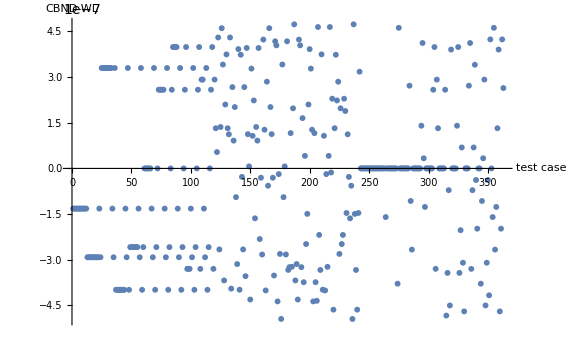

```mathematica
ListPlot[{out[[All, -2]]- out[[All, -1]]}, PlotRange->Full, ImageSize->Large, AxesLabel->{"test case", "CBND-WL"}]
```

```mathematica
TableForm[Reverse[SortBy[out, Abs[#[[-2]]-#[[-1]]] &]][[1;;10]], TableHeadings->{Range[10], {"a", "b", "ρ", "CBND", "WL"}}]
```

| a | b | ρ | CBND | WL
1 | 2 | -0.4 | 0.5 | 0.343764 | 0.343764
2 | -0.4 | 2 | 0.5 | 0.343764 | 0.343764
3 | 0.4 | 0.4 | -1 | 0.310843 | 0.310843
4 | 2 | 0 | 0.5 | 0.497974 | 0.497974
5 | 0 | 2 | 0.5 | 0.497974 | 0.497974
6 | 0.8 | 2 | -1 | 0.765394 | 0.765394
7 | 2 | 0.8 | -1 | 0.765394 | 0.765394
8 | 1.2 | 0.8 | 0.5 | 0.732731 | 0.732731
9 | 0.8 | 1.2 | 0.5 | 0.732731 | 0.732731
10 | 2 | 1.2 | 0.5 | 0.873401 | 0.873401

## Gaussian quadrature

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
GaussianQuadratureWeights[10, -Pi, Pi]
```

{{-3.05962,0.209454},{-2.71768,0.469515},{-2.13443,0.68828},{-1.36155,0.845926},{-0.467703,0.928417},{0.467703,0.928417},{1.36155,0.845926},{2.13443,0.68828},{2.71768,0.469515},{3.05962,0.209454}}

```mathematica
GaussianQuadratureWeights[10, -Pi,fd[ Pi, <|"ub"->1|>]]
```

{{fd[-3.05962,<|ub→0.0130467|>],fd[0.209454,<|ub→0.0333357|>]},{fd[-2.71768,<|ub→0.0674683|>],fd[0.469515,<|ub→0.0747257|>]},{fd[-2.13443,<|ub→0.160295|>],fd[0.68828,<|ub→0.109543|>]},{fd[-1.36155,<|ub→0.283302|>],fd[0.845926,<|ub→0.134633|>]},{fd[-0.467703,<|ub→0.425563|>],fd[0.928417,<|ub→0.147762|>]},{fd[0.467703,<|ub→0.574437|>],fd[0.928417,<|ub→0.147762|>]},{fd[1.36155,<|ub→0.716698|>],fd[0.845926,<|ub→0.134633|>]},{fd[2.13443,<|ub→0.839705|>],fd[0.68828,<|ub→0.109543|>]},{fd[2.71768,<|ub→0.932532|>],fd[0.469515,<|ub→0.0747257|>]},{fd[3.05962,<|ub→0.986953|>],fd[0.209454,<|ub→0.0333357|>]}}

```mathematica
fd[#, <|"ub"->1|>] & /@ Subdivide[-Pi/4, Pi/3, 10]
```

{fd[-π/4,<|ub→1|>],fd[-(23 π)/120,<|ub→1|>],fd[-(2 π)/15,<|ub→1|>],fd[-(3 π)/40,<|ub→1|>],fd[-π/60,<|ub→1|>],fd[π/24,<|ub→1|>],fd[π/10,<|ub→1|>],fd[(19 π)/120,<|ub→1|>],fd[(13 π)/60,<|ub→1|>],fd[(11 π)/40,<|ub→1|>],fd[π/3,<|ub→1|>]}

```mathematica
Module[{ub=#, pw, out},
pw=GaussianQuadratureWeights[10, -Pi/4, ub];
out=Total[Function[entry, entry[[2]] Cos[ub+entry[[1]]]][#] & /@ pw]- N[ Sin[2 ub]-Sin[ub-Pi/4]];
out
] & /@ (fd[#, <|"ub"->1|>] & /@ Subdivide[-Pi/4, Pi/3, 10])
```

{fd[0.,<|ub→6.12323×10^-17|>],fd[-6.245×10^-17,<|ub→0.|>],fd[0.,<|ub→-2.22045×10^-16|>],fd[-1.11022×10^-16,<|ub→-2.22045×10^-16|>],fd[-1.11022×10^-16,<|ub→0.|>],fd[0.,<|ub→2.22045×10^-16|>],fd[0.,<|ub→2.22045×10^-16|>],fd[0.,<|ub→4.996×10^-16|>],fd[0.,<|ub→2.22045×10^-16|>],fd[-3.33067×10^-16,<|ub→0.|>],fd[2.22045×10^-16,<|ub→-2.22045×10^-16|>]}

```mathematica
Integrate[Exp[3 x1 -x2] Cos[t2+x2], {x1, -Infinity, t1}, {x2, -Pi/4, t2}]
```

1/6 ⅇ^(3 t1-t2) (√2 ⅇ^(π/4+t2) Cos[t2]-Cos[2 t2]+Sin[2 t2])

```mathematica
Integrate[Exp[3 x1 -x2] Cos[t2+x2], {x1, -100, t1}, {x2, -Pi/4, t2}]
```

1/6 ⅇ^(-300-t2) (-1+ⅇ^(300+3 t1)) (√2 ⅇ^(π/4+t2) Cos[t2]-Cos[2 t2]+Sin[2 t2])

```mathematica
out=Module[{upperBounds, pw, t1, t2},
upperBounds=Flatten[Outer[List, fd[#, <|"ub1"->1|>] & /@ Subdivide[-5., 5., 10], fd[#, <|"ub2"->1|>] & /@ Subdivide[-Pi/4, Pi/3, 10], 1, 1], 1];
pw={{#[[1]], #[[2]]}, Flatten[Outer[List, GaussianQuadratureWeights[32, -100, #[[1]]], GaussianQuadratureWeights[32, -Pi/4, #[[2]]], 1, 1], 1]} & /@ upperBounds;
Function[entry, {entry[[1, 1]], entry[[1, 2]], Total[#[[1, 2]] #[[2, 2]]Exp[3 #[[1, 1]]-#[[2, 1]]] Cos[entry[[1, 2]]+#[[2, 1]]] & /@ entry[[2]]], (1/6 ⅇ^(-300-t2) (-1+ⅇ^(300+3 t1)) (√2 ⅇ^(π/4+t2) Cos[t2]-Cos[2 t2]+Sin[2 t2]) /. {t1->entry[[1,1]], t2->entry[[1,2]]})}][#] & /@ pw
];
```

$Aborted

```mathematica
bigPhi[{0}, {{1}}, {0}]
```

0.5

```mathematica
bigPhi[{0, 0}, {{1, 0}, {0, 1}}, {0, -10}]
```

0.

```mathematica
CDF[MultinormalDistribution[{0, 0}, {{1, 0}, {0, 1}}], {0, -10.}]
```

3.80993×10^-24

```mathematica
bigPhi[{0, 0}, {{0.5 0.5 , fd[-0.9, <|"rho"->1|>] 0.5  0.3}, {fd[-0.9, <|"rho"->1|>] 0.5  0.3, 0.3 0.3}},  {-0.1, 0.1}]
```

General::munfl: Exp[-997.248] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-991.245] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

fd[0.0978398,<|rho→0.336424|>]

```mathematica
CDF[MultinormalDistribution[{0, 0}, {{0.5 0.5 , -0.9 0.5  0.3}, {-0.9 0.5  0.3, 0.3 0.3}}], {-0.1, 0.1}]
```

0.0978398

```mathematica
CDF[MultinormalDistribution[{0, 0, 0}, {{0.5 0.5 , -0.999 0.5  0.2, -0.8 0.5 0.6}, {-0.999 0.5  0.2, 0.2 0.2, 0.35 0.2 0.6}, {-0.8 0.5 0.6, 0.35 0.2 0.6, 0.6 0.6}}], {-0.04, 0.1, 0.06}]
```

MultinormalDistribution::posdefprm: The value {{0.25,-0.0999,-0.24},{-0.0999,0.04,0.042},{-0.24,0.042,0.36}} at position 2 in MultinormalDistribution[{0,0,0},{{0.25,-0.0999,-0.24},{-0.0999,0.04,0.042},{-0.24,0.042,0.36}}] is expected to be a symmetric positive definite matrix.

CDF[MultinormalDistribution[{0,0,0},{{0.25,-0.0999,-0.24},{-0.0999,0.04,0.042},{-0.24,0.042,0.36}}],{-0.04,0.1,0.06}]

```mathematica
bigPhi[{0, 0, 0}, {{0.5 0.5 , -0.95 0.5  0.3, -0.6 0.5 0.6}, {-0.95 0.5  0.3, 0.3 0.3, 0.75 0.3 0.6}, {-0.6 0.5 0.6, 0.75 0.3 0.6, 0.6 0.6}}, {-0.04, 0.1, 0.06}]
```

General::munfl: Exp[-2642.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2646.47] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2653.34] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0796418

```mathematica
Module[{mean, vol1, vol2, vol3, rho12, rho13, rho23, covMat, x},
mean={0, 0, 0};
vol1=0.5;
vol2=0.3;
vol3=0.7;
rho12=-0.999;
rho13=-0.6;
rho23=0.6;
covMat={{vol1 vol1, rho12 vol1 vol2, rho13 vol1 vol3}, {rho12 vol1 vol2, vol2 vol2, rho23 vol2 vol3}, {rho13 vol1 vol3, rho23 vol2 vol3, vol3 vol3}};
x={-0.04, 0.1, 0.06};
{bigPhi[mean, covMat, x], CDF[MultinormalDistribution[mean, covMat], x]}
]
```

General::munfl: Exp[-99801.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-99800.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-99798.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0469507,0.0474907}